```mathematica
-
```

# Quadratic Soma Neuron Model

## Workspace

Model Equation Derivations

## Derivation of Quadratic Soma Model

This derivation tries to find a unified model of the quadratic soma that tries to account for what happens to I_lr as a function of V_r.  The hope is that with this derivation, we might have an all-inclusive model that accounts for when the neuron resets, as opposed to assuming that it always resets back to zero.

#### Circuit Schematic

```mathematica
ImageResize[Import["/home/noza/work/Schematic Pictures/SomaNoAnNoA6WithIrDrawing.png"],600]
```

-Graphics-

Compared to the image above, the following notations are used below, in the equations:

I_leak→I_l

I_bk→I_b

I_lkr→I_lr

### Basic Equations

#### Dimensionless quadratic soma model

τ_m OverDot[i_m]=1/2 i_m-i_m+i_in

#### Bias equations

Current mirror mirroring the leak current

I_l/α_7=I_lk/α_B1

Translinear principle to use the biases (I_in and I_lk) to set the output (I_m)

(I_m I_b)/(α_1 α_10)=(I_lk I_in)/(α_B1 α_B2)

Feedback current I_fb is a mirror of the output current (I_m)

(Note: this derivation assumes that transisor A_6 isn't in the circuit)

I_fb/α_4=I_m/α_3

Current mirror for the refractory current

I_r/α_12=I_ref/α_B3

#### Transistor device equations for important currents

Output current

I_m=α_1 I_(0_1)ⅇ^((-κ·V_mgs)/U_t)

I_m=α_1 I_(0_1)ⅇ^((κ·(V_dd-V_m))/U_t)

Another way to write this equation is as follows.  The reason for writing it this way is that it will be used during the derivation to write the linear region portion of the I_lr as a function of I_m.

I_m/(α_1 I_(0_1))=(ⅇ^((V_dd-V_m)/U_t))^κ
(I_m/(α_1 I_(0_1)))^(1/κ)=ⅇ^((V_dd-V_m)/U_t)
(I_m/(α_1 I_(0_1)))^(1/κ)=ⅇ^((-(V_m-V_dd))/U_t)
ⅇ^((V_m-V_d)/U_t)=(I_m/(α_1 I_(0_1)))^(-1/κ)

ⅇ^((V_m-V_d)/U_t)=((α_1 I_(0_1))/I_m)^(1/κ)

Refractory current

(Note: this transistor could/should operate in the linear region)

I_lr=α_8 I_(0_8)ⅇ^((-κ·V_lrgs)/U_t)(1-ⅇ^(V_lrds/U_t))

I_lr=α_8 I_(0_8)ⅇ^((κ·(V_dd-V_r))/U_t)(1-ⅇ^((V_m-V_dd)/U_t))

I_lr=I_lr_sat(1-ⅇ^((V_m-V_dd)/U_t))

We separate out just the I_lr_sat part of this equation because it is the only part that is dependent upon V_r.  Another way to think about this equation is that I_lr_sat is transistor A_8’s current output when the transistor is operating in the saturated region, as opposed to the ohmic (or linear) region.  In other words, I_lr is nothing more than I_lr_sat being tuned down in terms of current as the transistor starts to operate in the linear region.

I_lr_sat=α_8 I_(0_8)ⅇ^((κ·(V_dd-V_r))/U_t)

#### Calculation of derivative of transistor equations

The reason for these derivative calculations is that they allow us to analyze the charging and discharging of the two capacitors in our circuit (C_m and C_r).

In order to analyze the charging/discharging behavior of C_m, we first need to solve for (ⅆ V_m)/ⅆt.  In order to this, we start with Eq. 6.

I_m=α_1 I_(0_1)ⅇ^((κ·(V_dd-V_m))/U_t)
I_m=α_1 I_(0_1)ⅇ^((κ V_dd-κ V_m)/U_t)
I_m=α_1 I_(0_1)ⅇ^((κ V_dd)/U_t)ⅇ^((-κ V_m)/U_t)
(ⅆ I_m)/ⅆt=α_1 I_(0_1)ⅇ^((κ V_dd)/U_t)ⅇ^((-κ V_m)/U_t)(ⅆ((-κ V_m)/U_t))/ⅆt
(ⅆ I_m)/ⅆt=I_m-κ/U_t(ⅆ V_m)/ⅆt

OverDot[I_m]=-κ/U_t I_m OverDot[V_m]

OverDot[V_m]=-U_t/κ OverDot[I_m]/I_m

Similar to the analysis above for C_m, in order to analyze the charging/discharging behavior of C_r, we need to solve for (ⅆ V_r)/ⅆt.  We start with Eq. 9.

I_lr_sat=α_8 I_(0_8)ⅇ^((κ·(V_dd-V_r))/U_t)

(ⅆ I_lr_sat)/ⅆt=α_8 I_(0_8)ⅇ^((κ V_dd)/U_t)ⅇ^((-κ V_r)/U_t)(ⅆ((-κ V_r)/U_t))/ⅆt
(ⅆ I_lr_sat)/ⅆt=I_lr_sat-κ/U_t(ⅆ V_r)/ⅆt

OverDot[I_lr_sat]=-κ/U_t I_lr_sat OverDot[V_r]

OverDot[V_r]=-U_t/(κ I_lr_sat)OverDot[I_lr_sat]

#### Capacitor charging equations

Charging C_r with I_r

C_r OverDot[V_r]=I_r

C_r OverDot[V_r]=α_12/α_B3 I_ref

After integrating Eq. 14, you get Eq. 15 below, where:
	t_r is the duration of the refractory period
	V_r is the voltage at which we consider the refractory period to be over b/c V_m starts to decrease again

α_12/α_B3 I_ref=(C_r V_r)/t_r

Charging/discharging C_mwith I_l, I_lr, I_b, I_fb

C_m OverDot[V_m]=I_l+I_lr-I_b-I_fb

### Full-Blown Derivation

Below is the derivation for the quadratic soma model assuming only that κ = 1.  Other than this, the math is performed in as general a manner as possible.  In other words, I_lr_sat is not assumed to be a constant at any point in this derivation; instead it is always assumed to be a function of time.  We call this the full-blown derivation, because it has all of the gory details about how our two dynamical systems (thanks to the two capacitors) are related and how their math is interrelated).

We start with Eq. 16.

C_m OverDot[V_m]=I_l+I_lr-I_b-I_fb

Subsituting from Eq. 2, Eq. 3, Eq. 4, Eq. 8, and Eq. 9 above:

C_m OverDot[V_m]=α_7/α_B1 I_lk+I_lr_sat(1-ⅇ^((V_m-V_dd)/U_t))-(α_1 α_10)/(α_B1 α_B2)(I_lk I_in)/I_m-α_4/α_3 I_m

Next, we use Eq. 11 to subsitute out OverDot[V_m] and then multiply I_m across to the other side of the equation.

-(C_m U_t)/κ OverDot[I_m]/I_m=α_7/α_B1 I_lk+I_lr_sat(1-ⅇ^((V_m-V_dd)/U_t))-(α_1 α_10)/(α_B1 α_B2)(I_lk I_in)/I_m-α_4/α_3 I_m
-(C_m U_t)/κ OverDot[I_m]=I_m(α_7/α_B1 I_lk+I_lr_sat(1-ⅇ^((V_m-V_dd)/U_t)))-(α_1 α_10)/(α_B1 α_B2)I_lk I_in-α_4/α_3 I_m^2

We use Eq. 7 to make the substitution that puts everyting in terms of currents (in other words converts V_m to I_m in the linear region  portion of the equation).

-(C_m U_t)/κ OverDot[I_m]=I_m(α_7/α_B1 I_lk+I_lr_sat(1-((α_1 I_(0_1))/I_m)^(1/κ)))-(α_1 α_10)/(α_B1 α_B2)I_lk I_in-α_4/α_3 I_m^2

Now we divide both sides by I_lk and perform some simplifying math.

(C_m U_t)/(κ I_lk)OverDot[I_m]=-α_7/α_B1 I_m-I_lr_sat/I_lk I_m+(I_lr_sat I_m)/I_lk((α_1 I_(0_1))/I_m)^(1/κ)+(α_1 α_10)/(α_B1 α_B2)I_in+α_4/α_3 I_m^2/I_lk
(C_m U_t)/(κ I_lk)OverDot[I_m]=-α_7/α_B1 I_m-I_lr_sat/I_lk I_m+I_lr_sat/I_lk(I_m^(1-1/κ)(α_1 I_(0_1)))^(1/κ)+(α_1 α_10)/(α_B1 α_B2)I_in+α_4/α_3 I_m^2/I_lk

For the sake of ease of computation, the next thing we do is assume that κ=1 in the exponents.  Without this approximation, the math gets very hairy and doesn’t provide any insights or intuition.  More specifically, we aren’t able to calculate/derive a dimensionless i_m value where the derivative is a simple, linear function of I_m.

(C_m U_t)/(κ I_lk)OverDot[I_m]=α_4/α_3 I_m^2/I_lk+I_lr_sat/I_lk(I_m^(1-1/1)(α_1 I_(0_1)))^(1/1)+(α_1 α_10)/(α_B1 α_B2)I_in-(α_7/α_B1+I_lr_sat/I_lk)I_m
(C_m U_t)/(κ I_lk)OverDot[I_m]=α_4/α_3 I_m^2/I_lk+α_1(I_lr_sat I_(0_1))/I_lk+(α_1 α_10)/(α_B1 α_B2)I_in-(α_7/α_B1+I_lr_sat/I_lk)I_m
(C_m U_t)/(κ I_lk)OverDot[I_m]=α_4/α_3 I_m^2/I_lk+α_1(I_lr_sat I_(0_1))/I_lk+(α_1 α_10)/(α_B1 α_B2)I_in-((α_7 I_lk+α_B1 I_lr_sat)/(α_B1 I_lk) )I_m

η=(α_7 I_lk+α_B1 I_lr_sat)/(α_B1 I_lk)

(C_m U_t)/(κ I_lk)OverDot[I_m]=α_4/α_3 I_m^2/I_lk+α_1(I_lr_sat I_(0_1))/I_lk+(α_1 α_10)/(α_B1 α_B2)I_in-η I_m

Next we divide both sides of the equation by η.  This allows us to isolate I_m so that we can later add the exact “coefficient” in front of it to turn the whole equation to something dimensionless.  Note: At this point in the derivation, the dimensions of each of the components of the equation is in terms of current.

(C_m U_t)/(κ I_lk)OverDot[I_m]/η=α_4/α_3 I_m^2/(η I_lk)+α_1(I_lr_sat I_(0_1))/(η I_lk)+(α_1 α_10)/(α_B1 α_B2)I_in/η-I_m
(C_m U_t)/(κ I_lk)OverDot[I_m]/η=1/2(2 α_4)/(α_3 η I_lk)I_m^2+α_1(I_lr_sat I_(0_1))/(η I_lk)+(α_1 α_10)/(α_B1 α_B2)I_in/η-I_m

β=(2 α_4)/(α_3 η I_lk)=(2 α_4 α_B1)/(α_3(α_7 I_lk+α_B1 I_lr_sat))

(C_m U_t)/(κ I_lk)OverDot[I_m]/η=1/2 β I_m^2+α_1(I_lr_sat I_(0_1))/(η I_lk)+(α_1 α_10)/(α_B1 α_B2)I_in/η-I_m

It should be noted that we multiplied the I_m^2 term by 1/2*2 so that we could eventually have the formula written in the form 1/2 i_m^2.  After this last step, we multiply both sides of the equation by β, which eventually allows us to turn everything dimensionless.

(C_m U_t)/(κ I_lk)(β OverDot[I_m])/η=1/2 (β I_m)^2+α_1(β I_lr_sat I_(0_1))/(η I_lk)+(α_1 α_10)/(α_B1 α_B2)(β I_in)/η-β I_m

Before we can make the equation above dimensionless, we need to solve for what OverDot[i_m] equals.

i_m=β I_m

i_m=(2 α_4 α_B1)/(α_3(α_7 I_lk+α_B1 I_lr_sat))I_m
OverDot[i_m]=(2 α_4 α_B1)/(α_3(α_7 I_lk+α_B1 I_lr_sat))OverDot[I_m]-(2 α_4 α_B1^2 I_m)/(α_3(α_7 I_lk+α_B1 I_lr_sat))^2 OverDot[I_lr_sat]
OverDot[i_m]=β OverDot[I_m]-(β α_B1 I_m)/(α_7 I_lk+α_B1 I_lr_sat)OverDot[I_lr_sat]

Using Eq. 20, we get:

OverDot[i_m]=β OverDot[I_m]-(α_B1 i_m)/(α_7 I_lk+α_B1 I_lr_sat)OverDot[I_lr_sat]
β OverDot[I_m]=OverDot[i_m]+(α_B1 i_m)/(α_7 I_lk+α_B1 I_lr_sat)OverDot[I_lr_sat]

β OverDot[I_m]=OverDot[i_m]+i_m/(η I_lk)OverDot[I_lr_sat]

Continuing the math from Eq. 19, we use Eq. 20 and Eq. 21 to make everything dimensionless:

(C_m U_t)/(κ I_lk)(OverDot[i_m]+i_m/(η I_lk)OverDot[I_lr_sat])/η=1/2 i_m^2+α_1(β I_lr_sat I_(0_1))/(η I_lk)+(α_1 α_10)/(α_B1 α_B2)(β I_in)/η-i_m
(C_m U_t)/(κ I_lk)(OverDot[i_m]/η+i_m/(η^2 I_lk)OverDot[I_lr_sat])=1/2 i_m^2-i_m+α_1(β I_lr_sat I_(0_1))/(η I_lk)+(α_1 α_10)/(α_B1 α_B2)(β I_in)/η

We expand the β and η terms and simplify:

(C_m U_t)/(κ I_lk)(OverDot[i_m]/((α_7 I_lk+α_B1 I_lr_sat)/(α_B1 I_lk))+i_m/(((α_7 I_lk+α_B1 I_lr_sat)/(α_B1 I_lk))^2 I_lk)OverDot[I_lr_sat])=1/2 i_m^2-i_m+α_1(((2 α_4 α_B1)/(α_3(α_7 I_lk+α_B1 I_lr_sat))) I_lr_sat I_(0_1))/((α_7 I_lk+α_B1 I_lr_sat)/(α_B1 I_lk) I_lk)+(α_1 α_10)/(α_B1 α_B2)(((2 α_4 α_B1)/(α_3(α_7 I_lk+α_B1 I_lr_sat))) I_in)/((α_7 I_lk+α_B1 I_lr_sat)/(α_B1 I_lk))
(C_m U_t α_B1 I_lk)/(κ I_lk(α_7 I_lk+α_B1 I_lr_sat))OverDot[i_m]+(C_m(U_t(α_B1 I_lk))^2)/(κ (I_lk^2(α_7 I_lk+α_B1 I_lr_sat))^2)i_m OverDot[I_lr_sat]=1/2 i_m^2-i_m+α_1(2 α_4 α_B1^2 I_lr_sat I_(0_1))/(α_3(α_7 I_lk+α_B1 I_lr_sat))^2+(α_1 α_10)/(α_B1 α_B2)(2 α_4 α_B1^2 I_in I_lk)/(α_3(α_7 I_lk+α_B1 I_lr_sat))^2
(α_B1 C_m U_t)/(α_7 κ (I_lk+α_B1/α_7 I_lr_sat))OverDot[i_m]+(α_B1^2 C_m U_t)/(α_7^2 κ)OverDot[I_lr_sat/(I_lk+α_B1/α_7 I_lr_sat)^2]i_m=1/2 i_m^2-i_m+(2 α_1 α_4 α_B1^2)/(α_3 α_7^2)(I_lr_sat I_(0_1))/(I_lk+α_B1/α_7 I_lr_sat)^2+(2 α_1 α_10 α_4 α_B1)/(α_B2 α_3 α_7^2)(I_in I_lk)/(I_lk+α_B1/α_7 I_lr_sat)^2
(α_B1 C_m U_t)/(α_7 κ (I_lk+α_B1/α_7 I_lr_sat))OverDot[i_m]=1/2 i_m^2-i_m(1+(α_B1^2 C_m U_t)/(α_7^2 κ)OverDot[I_lr_sat/(I_lk+α_B1/α_7 I_lr_sat)^2])+(2 α_1 α_4 α_B1^2)/(α_3 α_7^2)(I_lr_sat I_(0_1))/(I_lk+α_B1/α_7 I_lr_sat)^2+(2 α_1 α_10 α_4 α_B1)/(α_B2 α_3 α_7^2)(I_in I_lk)/(I_lk+α_B1/α_7 I_lr_sat)^2

Combining Eq. 13 and Eq. 14, we know that

(C_r U_t)/(κ I_lr_sat)OverDot[I_lr_sat]=-α_12/α_B3 I_ref
OverDot[I_lr_sat]=-(α_12 κ)/(α_B3 C_r U_t)I_ref I_lr_sat
OverDot[I_lr_sat]=-ρ_ref I_ref I_lr_sat

Which we can now substitute back into the full equation

(α_B1 C_m U_t)/(α_7 κ (I_lk+α_B1/α_7 I_lr_sat))OverDot[i_m]=1/2 i_m^2-i_m(1+(α_B1^2 C_m U_t)/(α_7^2 κ)(-(α_12 κ)/(α_B3 C_r U_t)I_ref I_lr_sat)/(I_lk+α_B1/α_7 I_lr_sat)^2)+(2 α_1 α_4 α_B1^2)/(α_3 α_7^2)(I_lr_sat I_(0_1))/(I_lk+α_B1/α_7 I_lr_sat)^2+(2 α_1 α_10 α_4 α_B1)/(α_B2 α_3 α_7^2)(I_in I_lk)/(I_lk+α_B1/α_7 I_lr_sat)^2
(α_B1 C_m U_t)/(α_7 κ (I_lk+α_B1/α_7 I_lr_sat))OverDot[i_m]=1/2 i_m^2-i_m(1-(α_B1^2 α_12 κ C_m U_t)/(α_7^2 α_B3 κ C_r U_t)(I_ref I_lr_sat)/(I_lk+α_B1/α_7 I_lr_sat)^2)+(2 α_1 α_4 α_B1^2)/(α_3 α_7^2)(I_lr_sat I_(0_1))/(I_lk+α_B1/α_7 I_lr_sat)^2+(2 α_1 α_10 α_4 α_B1)/(α_B2 α_3 α_7^2)(I_in I_lk)/(I_lk+α_B1/α_7 I_lr_sat)^2
(α_B1 C_m U_t)/(α_7 κ (I_lk+α_B1/α_7 I_lr_sat))OverDot[i_m]=1/2 i_m^2-i_m(1-(α_B1^2 α_12 C_m)/(α_7^2 α_B3 C_r)(I_ref I_lr_sat)/(I_lk+α_B1/α_7 I_lr_sat)^2)+(2 α_1 α_4 α_B1^2)/(α_3 α_7^2)(I_lr_sat I_(0_1))/(I_lk+α_B1/α_7 I_lr_sat)^2+(2 α_1 α_10 α_4 α_B1)/(α_B2 α_3 α_7^2)(I_in I_lk)/(I_lk+α_B1/α_7 I_lr_sat)^2

ρ_tau/(I_lk+ρ_ilkr I_lr_sat)OverDot[i_m]=1/2 i_m^2-i_m(1-ρ_a(I_ref I_lr_sat)/(I_lk+ρ_ilkr I_lr_sat)^2)+ρ_b(I_lr_sat I_(0_1))/(I_lk+ρ_ilkr I_lr_sat)^2+ρ_qua(I_in I_lk)/(I_lk+ρ_ilkr I_lr_sat)^2

### Full-Blown Implementation

This is the implementation section corresponding to the full-blown derivation above.

ρ_tau/(I_lk+ρ_ilkr I_lr_sat)OverDot[i_m]=1/2 i_m^2-i_m(1-ρ_a(I_ref I_lr_sat)/(I_lk+ρ_ilkr I_lr_sat)^2)+ρ_b(I_lr_sat I_(0_1))/(I_lk+ρ_ilkr I_lr_sat)^2+ρ_qua(I_in I_lk)/(I_lk+ρ_ilkr I_lr_sat)^2

```mathematica
f[τ_,iin_,iref_,ilr_]=1/Integrate[τ/(1/2 im^2-im(1+iref)+iin+ilr),{im,0,∞},Assumptions->iin>0.5&&iref>0&& ilr>0, GenerateConditions->False]
f[τ_,iin_,iref_,ilr_,β0_,βf_]=1/Integrate[τ/(1/2 im^2-im(1+iref)+iin+ilr),{im,β0,βf},Assumptions->iin>0.5&&iref>0&& ilr>0, GenerateConditions->False]
```

1/(τ (π √(1/(2 iin+2 ilr-(iref+1)^2))-(2 tan^-1((-iref-1)/(√(2 iin+2 ilr-(iref+1)^2))))/(√(2 iin+2 ilr-(iref+1)^2))))

(√(2 iin+2 ilr-(iref+1)^2))/(τ (2 tan^-1((βf-iref-1)/(√(2 iin+2 ilr-(iref+1)^2)))-2 tan^-1((β0-iref-1)/(√(2 iin+2 ilr-(iref+1)^2)))))

#### Understanding how f is affected by i_in, i_ref, and i_lr

```mathematica
f==f[τ,Subscript[i, in],Subscript[i, ref],Subscript[i, lr]]
```

f==1/(τ (π √(1/(2 i_in+2 i_lr-(i_ref+1)^2))-(2 tan^-1((-i_ref-1)/(√(2 i_in+2 i_lr-(i_ref+1)^2))))/(√(2 i_in+2 i_lr-(i_ref+1)^2))))

```mathematica
Manipulate[
Plot[
f[tau,iin,iref,ilr],{iin,0,3},PlotRange->{{0,3},{0,100}},AxesLabel->{"i_in","f"}
],
{{tau,0.01},0.001,0.05,0.001,Appearance->{"Labeled","Open"}},
{{iref,0},0,10,0.1,Appearance->{"Labeled","Open"}},
{{ilr,0},0,10,0.1,Appearance->{"Labeled","Open"}}
]
```

#### Understanding how I_lr_sat behaves

```mathematica
Ilr[t_,Iref_,pref_,Ir0_]=Ilrsat[t]/.DSolve[{Ilrsat'[t]==-pref Iref Ilrsat[t],Ilrsat[0]==Ir0},Ilrsat[t],t]⟦1⟧
```

Ir0 ⅇ^(-Iref pref t)

```mathematica
Manipulate[
Grid[{
{Ilr[t]==Ilr[t,Iref,pref,Ir0]},
{Plot[Ilr[t,Iref,pref,Ir0],
{t,0,tMax},PlotRange->{0,1.1Ir0},ImageSize->Large,AxesLabel->{"t","I_lr_sat(t)"}
]}
}],
{{Iref,50.0},0.1,100,0.1,Appearance->{"Labeled","Open"}},
{{pref,0.1},0.01,5,0.01,Appearance->{"Labeled","Open"}},
{{Ir0,2},0.01,10,0.01,Appearance->{"Labeled","Open"}},
{{tMax,1},1,10,1.,Appearance->{"Labeled","Open"}}
]
```

#### Understanding of how i_m behaves

```mathematica
DSolve[{
ptau/(Ilk+pilkr Ilrsat[t])imem'[t]==1/2 imem[t]^2-imem[t](1-pfoo(Iref Ilrsat[t])/(Ilk+pilkr Ilrsat[t])^2)+pbar (Ilrsat[t] I01)/(Ilk+pilkr Ilrsat[t])^2+pqua(Iin Ilk)/(Ilk+pilkr Ilrsat[t])^2 ,
Ilrsat'[t]==-pref Iref Ilrsat[t]
},{imem[t],Ilrsat[t]},t]
```

```mathematica
DSolve[{
ptau/(Ilk+pilkr Ilrsat[t])imem'[t]==1/2 imem[t]^2-imem[t](1-pilr(Iref Ilrsat[t])/(Ilk+pilkr Ilrsat[t])^2)+pqua(Iin Ilk)/(Ilk+pilkr Ilrsat[t])^2 ,
Ilrsat'[t]==-pref Iref Ilrsat[t]
},{imem[t],Ilrsat[t]},t]
```

Solve::ifun: Inverse functions are being used by TraditionalForm`Solve, so some solutions may not be found; use Reduce for complete solution information.

DSolve[{(ptau imem'(t))/(Ilk+pilkr Ilrsat(t))==(Iin Ilk pqua)/(Ilk+pilkr Ilrsat(t))^2-imem(t) (1-(Iref pilr Ilrsat(t))/(Ilk+pilkr Ilrsat(t))^2)+(imem(t))^2/2,Ilrsat'(t)==-Iref pref Ilrsat(t)},{imem(t),Ilrsat(t)},t]

#### Fully exploded implementation of the derivation above

```mathematica
fullModelSol=DSolve[{
(αB1 Cm UT)/(α7 κ (Ilk+αB1/α7 Ilrsat[t])) imem'[t]==1/2 imem[t]^2-imem[t](1-(αB1^2 α12 Cm)/(α7^2 αB3 Cr)(Iref Ilrsat[t])/(Ilk+αB1/α7 Ilrsat[t])^2)+(2 α1 α4 αB1^2)/(α3 α7^2) (Ilrsat[t] I01)/(Ilk+αB1/α7 Ilrsat[t])^2+(2 α1 α10 α4 αB1)/(αB2 α3 α7^2) (Iin Ilk)/(Ilk+αB1/α7 Ilrsat[t])^2 ,
Ilrsat'[t]==-(α12 κ)/(αB3 Cr UT)Iref Ilrsat[t]
},{imem[t],Ilrsat[t]},t];
```

```mathematica
im[t_,Iin_,Ilk_,Iref_]=Simplify[imem[t]/.fullModelSol,t≥0&&α1>0&&α3>0&&α4>0&&α7>0&&α10>0&&α12>0&&αB1>0&&αB2>0&&αB3>0&&I01>0&&Iin≥I01&&Iin>0&&Ilk>0&&Iref>0&&Cm>0&&Cr>0&&UT>0&&κ>0];
Ilrsat[t_,Iref_]=Simplify[Ilrsat[t]/.fullModelSol,t≥0&&α1>0&&α3>0&&α4>0&&α7>0&&α10>0&&α12>0&&αB1>0&&αB2>0&&αB3>0&&I01>0&&Iin≥I01&&Iin>0&&Ilk>0&&Iref>0&&Cm>0&&Cr>0&&UT>0&&κ>0];
```

```mathematica
paramNameRules = {α1->"α_1",α3->"α_3",α4->"α_4",α7->"α_7",α8->"α_8",α10->"α_10",α12->"α_12",αB1->"α_B1",αB2->"α_B2",αB3->"α_B3",Cm->"C_m",Cr->"C_r",UT->"U_t",Iin->"I_in",Ilk->"I_lk",Iref->"I_ref",I01->"I_01",C[1]->"I_lr0"};
Subscript[i, lr_sat]==Ilrsat[t,"I_ref"]/.paramNameRules
Subscript[i, m]==im["t","I_in","I_lk","I_ref"]/.paramNameRules
```

i_lr_sat=={I_lr0 ⅇ^(-(κ α_12 I_ref t)/(α_B3 C_r U_t))}

i_m=={-((C_m C_r I_lr0 U_t (C_m I_ref α_12)^((C_r (I_lk α_7+√(I_lk (I_lk α_7^2-(4 I_in α_1 α_10 α_4 α_B1)/(α_3 α_B2)))) α_B3)/(2 C_m I_ref α_12 α_B1)) α_B1 α_B3 ((C_r I_lr0 α_B3 ⅇ^(-(I_ref α_12 t κ)/(C_r U_t α_B3)))/κ^2)^((C_r (√(I_lk (I_lk α_7^2-(4 I_in α_1 α_10 α_4 α_B1)/(α_3 α_B2)))-I_lk α_7) α_B3)/(2 C_m I_ref α_12 α_B1)-1) (ⅈ κ)^((C_r (√(I_lk (I_lk α_7^2-(4 I_in α_1 α_10 α_4 α_B1)/(α_3 α_B2)))-I_lk α_7) α_B3)/(C_m I_ref α_12 α_B1)) (-1/(C_m U_t α_B1 √(α_3 α_B2))I_lk^(1/2 ((C_r (I_lk α_7+√(I_lk (I_lk α_7^2-(4 I_in α_1 α_10 α_4 α_B1)/(α_3 α_B2)))) α_B3)/(C_m I_ref α_12 α_B1)+1)) (√(I_lk α_3 α_B2) α_7+√(I_lk α_3 α_7^2 α_B2-4 I_in α_1 α_10 α_4 α_B1)) (ⅈ κ)^((C_r (I_lk α_7+√(I_lk (I_lk α_7^2-(4 I_in α_1 α_10 α_4 α_B1)/(α_3 α_B2)))) α_B3)/(C_m I_ref α_12 α_B1)) κ (C_r (I_lk α_3 α_7 α_B2-2 I_01 α_1 α_4 α_B1 α_B2+√(I_lk α_3 α_B2 (I_lk α_3 α_7^2 α_B2-4 I_in α_1 α_10 α_4 α_B1))) α_B3)/(2 C_m I_ref α_12 α_3 α_B1 α_B2)(C_r √(I_lk α_3 α_B2 (I_lk α_3 α_7^2 α_B2-4 I_in α_1 α_10 α_4 α_B1)) α_B3)/(C_m I_ref α_12 α_3 α_B1 α_B2)+1(C_r I_lr0 α_B3 ⅇ^(-(I_ref α_12 t κ)/(C_r U_t α_B3)))/(C_m I_ref α_12) ((C_r I_lr0 α_B3 ⅇ^(-(I_ref α_12 t κ)/(C_r U_t α_B3)))/(C_m I_lk I_ref α_12 κ^2))^((C_r (I_lk α_7+√(I_lk (I_lk α_7^2-(4 I_in α_1 α_10 α_4 α_B1)/(α_3 α_B2)))) α_B3)/(2 C_m I_ref α_12 α_B1))-(I_ref α_12 (I_lk α_3 α_7 α_B2-2 I_01 α_1 α_4 α_B1 α_B2+√(I_lk α_3 α_B2 (I_lk α_3 α_7^2 α_B2-4 I_in α_1 α_10 α_4 α_B1))) ((C_r I_lr0 α_B3 ⅇ^(-(I_ref α_12 t κ)/(C_r U_t α_B3)))/(C_m I_ref α_12 κ^2))^((C_r (I_lk α_7+√(I_lk (I_lk α_7^2-(4 I_in α_1 α_10 α_4 α_B1)/(α_3 α_B2)))) α_B3)/(2 C_m I_ref α_12 α_B1)+1) (ⅈ κ)^((C_r (I_lk α_7+√(I_lk (I_lk α_7^2-(4 I_in α_1 α_10 α_4 α_B1)/(α_3 α_B2)))) α_B3)/(C_m I_ref α_12 α_B1)) κ^3 (2 C_m I_ref α_12 α_3 α_B1 α_B2+C_r (I_lk α_3 α_7 α_B2-2 I_01 α_1 α_4 α_B1 α_B2+√(I_lk α_3 α_B2 (I_lk α_3 α_7^2 α_B2-4 I_in α_1 α_10 α_4 α_B1))) α_B3)/(2 C_m I_ref α_12 α_3 α_B1 α_B2)(C_r √(I_lk α_3 α_B2 (I_lk α_3 α_7^2 α_B2-4 I_in α_1 α_10 α_4 α_B1)) α_B3)/(C_m I_ref α_12 α_3 α_B1 α_B2)+2(C_r I_lr0 α_B3 ⅇ^(-(I_ref α_12 t κ)/(C_r U_t α_B3)))/(C_m I_ref α_12))/(U_t (C_m I_ref α_12 α_3 α_B1 α_B2+C_r √(I_lk α_3 α_B2 (I_lk α_3 α_7^2 α_B2-4 I_in α_1 α_10 α_4 α_B1)) α_B3))+(ⅈ^((C_r (I_lk α_7-√(I_lk (I_lk α_7^2-(4 I_in α_1 α_10 α_4 α_B1)/(α_3 α_B2)))) α_B3)/(C_m I_ref α_12 α_B1)) C_m^((C_r (√(I_lk (I_lk α_7^2-(4 I_in α_1 α_10 α_4 α_B1)/(α_3 α_B2)))-I_lk α_7) α_B3)/(2 C_m I_ref α_12 α_B1)-1) I_ref α_12 ((C_r I_lr0 α_B3 ⅇ^(-(I_ref α_12 t κ)/(C_r U_t α_B3)))/(I_ref α_12 κ^2))^((C_r (I_lk α_7-√(I_lk (I_lk α_7^2-(4 I_in α_1 α_10 α_4 α_B1)/(α_3 α_B2)))) α_B3)/(2 C_m I_ref α_12 α_B1)+1) κ^((3 C_m I_ref α_12 α_B1+C_r I_lk α_7 α_B3-C_r √(I_lk (I_lk α_7^2-(4 I_in α_1 α_10 α_4 α_B1)/(α_3 α_B2))) α_B3)/(C_m I_ref α_12 α_B1)) c_2 ((C_m I_ref α_12 α_3 α_B1 α_B2 (√(I_lk (I_lk α_3 α_7^2 α_B2-4 I_in α_1 α_10 α_4 α_B1))-I_lk α_7 √(α_3 α_B2))-C_r I_lk (α_3 α_7 α_B2 (I_lk α_7 √(α_3 α_B2)-√(I_lk (I_lk α_3 α_7^2 α_B2-4 I_in α_1 α_10 α_4 α_B1)))-4 I_in α_1 α_10 α_4 α_B1 √(α_3 α_B2)) α_B3) ⅇ^((I_ref α_12 t κ)/(C_r U_t α_B3)) -(C_r (-I_lk α_3 α_7 α_B2+2 I_01 α_1 α_4 α_B1 α_B2+√(I_lk α_3 α_B2 (I_lk α_3 α_7^2 α_B2-4 I_in α_1 α_10 α_4 α_B1))) α_B3)/(2 C_m I_ref α_12 α_3 α_B1 α_B2)1-(C_r √(I_lk α_3 α_B2 (I_lk α_3 α_7^2 α_B2-4 I_in α_1 α_10 α_4 α_B1)) α_B3)/(C_m I_ref α_12 α_3 α_B1 α_B2)(C_r I_lr0 α_B3 ⅇ^(-(I_ref α_12 t κ)/(C_r U_t α_B3)))/(C_m I_ref α_12)+C_r I_lr0 √α_3 α_B1 α_B2 (-I_lk α_3 √α_B2 α_7+2 I_01 α_1 α_4 α_B1 √α_B2+√(I_lk α_3 (I_lk α_3 α_7^2 α_B2-4 I_in α_1 α_10 α_4 α_B1))) α_B3 (2 C_m I_ref α_12 α_3 α_B1 α_B2-C_r (-I_lk α_3 α_7 α_B2+2 I_01 α_1 α_4 α_B1 α_B2+√(I_lk α_3 α_B2 (I_lk α_3 α_7^2 α_B2-4 I_in α_1 α_10 α_4 α_B1))) α_B3)/(2 C_m I_ref α_12 α_3 α_B1 α_B2)2-(C_r √(I_lk α_3 α_B2 (I_lk α_3 α_7^2 α_B2-4 I_in α_1 α_10 α_4 α_B1)) α_B3)/(C_m I_ref α_12 α_3 α_B1 α_B2)(C_r I_lr0 α_B3 ⅇ^(-(I_ref α_12 t κ)/(C_r U_t α_B3)))/(C_m I_ref α_12)))/(C_r I_lr0 U_t α_B1 √(α_3 α_B2) α_B3 (C_m I_ref α_12 α_3 α_B1 α_B2-C_r √(I_lk α_3 α_B2 (I_lk α_3 α_7^2 α_B2-4 I_in α_1 α_10 α_4 α_B1)) α_B3))))/((I_lk ⅇ^((I_ref α_12 t κ)/(C_r U_t α_B3)) α_7+I_lr0 α_B1) κ^3 (c_2 -(C_r (-I_lk α_3 α_7 α_B2+2 I_01 α_1 α_4 α_B1 α_B2+√(I_lk α_3 α_B2 (I_lk α_3 α_7^2 α_B2-4 I_in α_1 α_10 α_4 α_B1))) α_B3)/(2 C_m I_ref α_12 α_3 α_B1 α_B2)1-(C_r √(I_lk α_3 α_B2 (I_lk α_3 α_7^2 α_B2-4 I_in α_1 α_10 α_4 α_B1)) α_B3)/(C_m I_ref α_12 α_3 α_B1 α_B2)(C_r I_lr0 α_B3 ⅇ^(-(I_ref α_12 t κ)/(C_r U_t α_B3)))/(C_m I_ref α_12) (C_m I_ref α_12)^((C_r √(I_lk (I_lk α_7^2-(4 I_in α_1 α_10 α_4 α_B1)/(α_3 α_B2))) α_B3)/(C_m I_ref α_12 α_B1))+((C_r I_lr0 α_B3 ⅇ^(-(I_ref α_12 t κ)/(C_r U_t α_B3)))/κ^2)^((C_r √(I_lk (I_lk α_7^2-(4 I_in α_1 α_10 α_4 α_B1)/(α_3 α_B2))) α_B3)/(C_m I_ref α_12 α_B1)) (ⅈ κ)^((2 C_r √(I_lk (I_lk α_7^2-(4 I_in α_1 α_10 α_4 α_B1)/(α_3 α_B2))) α_B3)/(C_m I_ref α_12 α_B1)) (C_r (I_lk α_3 α_7 α_B2-2 I_01 α_1 α_4 α_B1 α_B2+√(I_lk α_3 α_B2 (I_lk α_3 α_7^2 α_B2-4 I_in α_1 α_10 α_4 α_B1))) α_B3)/(2 C_m I_ref α_12 α_3 α_B1 α_B2)(C_r √(I_lk α_3 α_B2 (I_lk α_3 α_7^2 α_B2-4 I_in α_1 α_10 α_4 α_B1)) α_B3)/(C_m I_ref α_12 α_3 α_B1 α_B2)+1(C_r I_lr0 α_B3 ⅇ^(-(I_ref α_12 t κ)/(C_r U_t α_B3)))/(C_m I_ref α_12))))}

```mathematica
Subscript[i, lr_sat]==Ilrsat[t,"I_ref"]
Subscript[i, lr_sat]==Ilrsat[t,"I_ref"]/.{C[1]->"I_lr0",(α12 κ)/(αB3 Cr UT)->"ρ_ref"}
```

i_lr_sat=={c_1 ⅇ^(-(α12 κ I_ref t)/(αB3 Cr UT))}

i_lr_sat=={I_lr0 ⅇ^(-I_ref ρ_ref t)}

```mathematica
paramRules={α1->1,α3->1,α4->1,α7->1,α8->1,α10->1,α12->1,αB1->1,αB2->1,αB3->1,Cm->100*10^-15,Cr->50*10^-15,UT->0.025,κ->1,I01->10^-15,C[1]->100,C[2]->50};
```

```mathematica
Ilrsat[t,Iref]/.paramRules
im[t,Iin,Ilk,Iref]/.paramRules
```

{100 ⅇ^(-8.×10^14 Iref t)}

{-((1.25×10^-26 (-1)^((√(Ilk (Ilk-4 Iin))-Ilk)/(4 Iref)) 2^(-(3 (√(Ilk (Ilk-4 Iin))-Ilk))/Iref-(13 (Ilk+√(Ilk (Ilk-4 Iin))))/(4 Iref)+12) 5^(-(11 (√(Ilk (Ilk-4 Iin))-Ilk))/(4 Iref)-(13 (Ilk+√(Ilk (Ilk-4 Iin))))/(4 Iref)+11) (ⅇ^(-8.×10^14 Iref t))^((√(Ilk (Ilk-4 Iin))-Ilk)/(4 Iref)-1) Iref^((Ilk+√(Ilk (Ilk-4 Iin)))/(4 Iref)) (1/(Iref/10000000000000-(√(Ilk (Ilk-4 Iin)))/20000000000000)4.×10^14 (-1)^((Ilk-√(Ilk (Ilk-4 Iin)))/(4 Iref)) 2^(-(3 (Ilk-√(Ilk (Ilk-4 Iin))))/Iref-(13 (√(Ilk (Ilk-4 Iin))-Ilk))/(4 Iref)+1) 5^(-(11 (Ilk-√(Ilk (Ilk-4 Iin))))/(4 Iref)-(13 (√(Ilk (Ilk-4 Iin))-Ilk))/(4 Iref)+2) Iref (ⅇ^(8.×10^14 Iref t) (((√(Ilk (Ilk-4 Iin))-Ilk) Iref)/10000000000000-(Ilk (-4 Iin+Ilk-√(Ilk (Ilk-4 Iin))))/20000000000000) -(-Ilk+√(Ilk (Ilk-4 Iin))+1/500000000000000)/(4 Iref)1-(√(Ilk (Ilk-4 Iin)))/(2 Iref)(50 ⅇ^(-8.×10^14 Iref t))/Iref+((-Ilk+√(Ilk (Ilk-4 Iin))+1/500000000000000) (5000000000000 ((Ilk-√(Ilk (Ilk-4 Iin))-1/500000000000000)/20000000000000+Iref/5000000000000))/Iref2-(√(Ilk (Ilk-4 Iin)))/(2 Iref)(50 ⅇ^(-8.×10^14 Iref t))/Iref)/200000000000) ((ⅇ^(-8.×10^14 Iref t))/Iref)^((Ilk-√(Ilk (Ilk-4 Iin)))/(4 Iref)+1)-(40. (-1)^((Ilk+√(Ilk (Ilk-4 Iin)))/(4 Iref)) 50^((Ilk+√(Ilk (Ilk-4 Iin)))/(4 Iref)+1) (Ilk+√(Ilk (Ilk-4 Iin))-1/500000000000000) Iref (5000000000000 ((Ilk+√(Ilk (Ilk-4 Iin))-1/500000000000000)/20000000000000+Iref/5000000000000))/Iref(√(Ilk (Ilk-4 Iin)))/(2 Iref)+2(50 ⅇ^(-8.×10^14 Iref t))/Iref ((ⅇ^(-8.×10^14 Iref t))/Iref)^((Ilk+√(Ilk (Ilk-4 Iin)))/(4 Iref)+1))/(Iref/10000000000000+(√(Ilk (Ilk-4 Iin)))/20000000000000)-4.×10^14 (-2)^((Ilk+√(Ilk (Ilk-4 Iin)))/(4 Iref)) 5^((Ilk+√(Ilk (Ilk-4 Iin)))/(2 Iref)) Ilk^(1/2 ((Ilk+√(Ilk (Ilk-4 Iin)))/(2 Iref)+1)) (√Ilk+√(Ilk-4 Iin)) ((ⅇ^(-8.×10^14 Iref t))/(Ilk Iref))^((Ilk+√(Ilk (Ilk-4 Iin)))/(4 Iref)) (Ilk+√(Ilk (Ilk-4 Iin))-1/500000000000000)/(4 Iref)(√(Ilk (Ilk-4 Iin)))/(2 Iref)+1(50 ⅇ^(-8.×10^14 Iref t))/Iref))/((ⅇ^(8.×10^14 Iref t) Ilk+100) ((ⅈ/64)^((√(Ilk (Ilk-4 Iin)))/Iref) 5^(-(11 √(Ilk (Ilk-4 Iin)))/(2 Iref)) (Ilk+√(Ilk (Ilk-4 Iin))-1/500000000000000)/(4 Iref)(√(Ilk (Ilk-4 Iin)))/(2 Iref)+1(50 ⅇ^(-8.×10^14 Iref t))/Iref (ⅇ^(-8.×10^14 Iref t))^((√(Ilk (Ilk-4 Iin)))/(2 Iref))+2^(1-(13 √(Ilk (Ilk-4 Iin)))/(2 Iref)) 5^(2-(13 √(Ilk (Ilk-4 Iin)))/(2 Iref)) Iref^((√(Ilk (Ilk-4 Iin)))/(2 Iref)) -(-Ilk+√(Ilk (Ilk-4 Iin))+1/500000000000000)/(4 Iref)1-(√(Ilk (Ilk-4 Iin)))/(2 Iref)(50 ⅇ^(-8.×10^14 Iref t))/Iref)))}

```mathematica
aDummy=B3*C3
```

B3 C3

```mathematica
aDummy^2
(aDummy/.{B3 C3->α3})^2
```

B3^2 C3^2

α3^2

```mathematica
Manipulate[
Grid[{{
Plot[Re[im[t,Iin*10^IinScale,Ilk*10^IlkScale,Iref*10^IrefScale]/.paramRules],{t,0,2},ImageSize->Large,PlotRange->{0,All},AxesLabel->{"t","i_m"}],
Plot[Ilrsat[t,Iref*10^IrefScale]/.paramRules,{t,0,0.2},ImageSize->Large,PlotRange->{0,All},AxesLabel->{"t","I_lrsat"}](*,
Plot[Im[im[t,Iin,Ilk,Iref]/.paramRules],{t,0,2},ImageSize->Large,PlotRange->All,AxesLabel->{"t","i_m"}]*)
}}],
{{Iin,1},0.1,10,0.1,Appearance->{"Labeled","Open"}},
{{IinScale,-10},-15,-1,1,Appearance->{"Labeled","Open"}},
{{Ilk,1},0.1,10,0.1,Appearance->{"Labeled","Open"}},
{{IlkScale,-10},-15,-1,1,Appearance->{"Labeled","Open"}},
{{Iref,1},0,10,0.5,Appearance->{"Labeled","Open"}},
{{IrefScale,-12},-15,-1,1,Appearance->{"Labeled","Open"}}
]
```

### Revised two dynamical system-based derivation

The reason for this new derivation is because I talked to Ben and he mentioned how another way to think about the derivation is to fix the threshold value in the derivation (instead of making it a function of I_lr_sat), and then model any change around that point as a variable of the I_lr_sat’s dynamical system.  He started to give me the intuition for how to think about the math in order to rederive the math using this idea.

We start with Eq. 16.

C_m OverDot[V_m]=I_l+I_lr-I_b-I_fb

Subsituting from Eq. 2, Eq. 3, Eq. 4, Eq. 8, and Eq. 9 above:

C_m OverDot[V_m]=α_7/α_B1 I_lk+I_lr_sat(1-ⅇ^((V_m-V_dd)/U_t))-(α_1 α_10)/(α_B1 α_B2)(I_lk I_in)/I_m-α_4/α_3 I_m

Next, we use Eq. 11 to subsitute out OverDot[V_m] and then multiply I_m across to the other side of the equation.

-(C_m U_t)/κ OverDot[I_m]/I_m=α_7/α_B1 I_lk+I_lr_sat(1-ⅇ^((V_m-V_dd)/U_t))-(α_1 α_10)/(α_B1 α_B2)(I_lk I_in)/I_m-α_4/α_3 I_m
-(C_m U_t)/κ OverDot[I_m]=I_m(α_7/α_B1 I_lk+I_lr_sat(1-ⅇ^((V_m-V_dd)/U_t)))-(α_1 α_10)/(α_B1 α_B2)I_lk I_in-α_4/α_3 I_m^2

We use Eq. 7 to make the substitution that puts everyting in terms of currents (in other words converts V_m to I_m in the linear region  portion of the equation).

-(C_m U_t)/κ OverDot[I_m]=I_m(α_7/α_B1 I_lk+I_lr_sat(1-((α_1 I_(0_1))/I_m)^(1/κ)))-(α_1 α_10)/(α_B1 α_B2)I_lk I_in-α_4/α_3 I_m^2

Now we divide both sides by I_lk and perform some simplifying math.

(C_m U_t)/(κ I_lk)OverDot[I_m]=-α_7/α_B1 I_m-I_lr_sat/I_lk I_m+(I_lr_sat I_m)/I_lk((α_1 I_(0_1))/I_m)^(1/κ)+(α_1 α_10)/(α_B1 α_B2)I_in+α_4/α_3 I_m^2/I_lk
(C_m U_t)/(κ I_lk)OverDot[I_m]=-α_7/α_B1 I_m-I_lr_sat/I_lk I_m+I_lr_sat/I_lk(I_m^(1-1/κ)(α_1 I_(0_1)))^(1/κ)+(α_1 α_10)/(α_B1 α_B2)I_in+α_4/α_3 I_m^2/I_lk

For the sake of ease of computation, the next thing we do is assume that κ=1 in the exponents.  Without this approximation, the math gets very hairy and doesn’t provide any insights or intuition.  More specifically, we aren’t able to calculate/derive a dimensionless i_m value where the derivative is a simple, linear function of I_m.

(C_m U_t)/(κ I_lk)OverDot[I_m]=α_4/α_3 I_m^2/I_lk+I_lr_sat/I_lk(I_m^(1-1/1)(α_1 I_(0_1)))^(1/1)+(α_1 α_10)/(α_B1 α_B2)I_in-(α_7/α_B1+I_lr_sat/I_lk)I_m
(C_m U_t)/(κ I_lk)OverDot[I_m]=α_4/α_3 I_m^2/I_lk+α_1(I_lr_sat I_(0_1))/I_lk+(α_1 α_10)/(α_B1 α_B2)I_in-(α_7/α_B1+I_lr_sat/I_lk)I_m
(C_m U_t)/(κ I_lk)OverDot[I_m]=α_4/α_3 I_m^2/I_lk+α_1(I_lr_sat I_(0_1))/I_lk+(α_1 α_10)/(α_B1 α_B2)I_in-((α_7 I_lk+α_B1 I_lr_sat)/(α_B1 I_lk) )I_m
(C_m U_t)/(κ I_lk)OverDot[I_m]=α_4/α_3 I_m^2/I_lk+α_1(I_lr_sat I_(0_1))/I_lk+(α_1 α_10)/(α_B1 α_B2)I_in-α_7/α_B1 I_m-(α_B1 I_lr_sat)/(α_B1 I_lk)I_m
α_B1/α_7(C_m U_t)/(κ I_lk)OverDot[I_m]=(α_4 α_B1)/(α_3 α_7) I_m^2/I_lk+(α_1 α_B1)/α_7(I_lr_sat I_(0_1))/I_lk+(α_1 α_10)/(α_B2 α_7)I_in-I_m-(α_B1 I_lr_sat)/(α_7 I_lk)I_m
α_B1/α_7(C_m U_t)/(κ I_lk)OverDot[I_m]=1/2(2 α_4 α_B1)/(α_3 α_7) I_m^2/I_lk+(α_1 α_B1)/α_7(I_lr_sat I_(0_1))/I_lk+(α_1 α_10)/(α_B2 α_7)I_in-I_m-(α_B1 I_lr_sat)/(α_7 I_lk)I_m

β = (2 α_4 α_B1)/(α_3 α_7 I_lk)

α_B1/α_7(C_m U_t)/(κ I_lk)OverDot[I_m]=1/2 β I_m^2+(α_1 α_B1)/α_7(I_lr_sat I_(0_1))/I_lk+(α_1 α_10)/(α_B2 α_7)I_in-I_m-(α_B1 I_lr_sat)/(α_7 I_lk)I_m
α_B1/α_7(C_m U_t)/(κ I_lk)β OverDot[I_m]=1/2(β I_m)^2+(α_1 α_B1)/α_7(β I_lr_sat I_(0_1))/I_lk+(α_1 α_10)/(α_B2 α_7)β I_in-β I_m-(α_B1 I_lr_sat)/(α_7 I_lk)β I_m

i_m= β I_m
	OverDot[i_m]= β OverDot[I_m]

α_B1/α_7(C_m U_t)/(κ I_lk)OverDot[i_m]=1/2 i_m^2+(α_1 α_B1)/α_7(β I_lr_sat I_(0_1))/I_lk+(α_1 α_10)/(α_B2 α_7)β I_in-i_m-(α_B1 I_lr_sat)/(α_7 I_lk)i_m
α_B1/α_7(C_m U_t)/(κ I_lk)OverDot[i_m]=1/2 i_m^2+(2 α_1 α_4 α_B1^2 I_(0_1))/(α_3 α_7^2 I_lk)I_lr_sat/I_lk+(2 α_1 α_10 α_4 α_B1)/(α_3 α_7^2 α_B2) I_in/I_lk-i_m-(α_B1 I_lr_sat)/(α_7 I_lk)i_m

i_lr_sat=η I_lr_sat
	OverDot[i_lr_sat]=η OverDot[I_lr_sat]
	η=α_B1/(α_7 I_lk)

α_B1/α_7(C_m U_t)/(κ I_lk)OverDot[i_m]=1/2 i_m^2+(2 α_1 α_4 α_B1 I_(0_1))/(α_3 α_7 I_lk)i_lr_sat+(2 α_1 α_10 α_4 α_B1)/(α_3 α_7^2 α_B2) I_in/I_lk-i_m(1+i_lr_sat)

τ_m OverDot[i_m]=1/2 i_m^2-i_m(1+i_lr_sat)+i_in+(2 α_1 α_4 α_B1 I_(0_1))/(α_3 α_7 I_lk)i_lr_sat
	i_in=(2 α_1 α_10 α_4 α_B1)/(α_3 α_7^2 α_B2) I_in/I_lk
	τ_m=α_B1/α_7(C_m U_t)/(κ I_lk)

OR

α_B1/α_7(C_m U_t)/(κ I_lk)OverDot[i_m]=1/2 i_m^2+(2 α_1 α_10 α_4 α_B1)/(α_3 α_7^2 α_B2) (((α_7 α_B2)/α_10 I_(0_1)i_lr_sat+I_in)/I_lk)-i_m(1+i_lr_sat)

Combining Eq. 13 and Eq. 14, we know that

(C_r U_t)/(κ I_lr_sat)OverDot[I_lr_sat]=-α_12/α_B3 I_ref
(α_B3 C_r U_t)/(α_12 κ)OverDot[I_lr_sat]=-I_ref I_lr_sat
(α_B3 C_r U_t)/(α_12 κ)η OverDot[I_lr_sat]=-I_refη I_lr_sat
(α_B3 C_r U_t)/(α_12 κ)OverDot[i_lr_sat]=-I_ref i_lr_sat
(α_B3 C_r U_t)/(α_12 κ I_ref)OverDot[i_lr_sat]=-i_lr_sat

τ_ref OverDot[i_lr_sat]=-i_lr_sat
	τ_ref=(α_B3 C_r U_t)/(α_12 κ I_ref)

### Revised two dynamical system-based implementation

#### Understanding of how i_m behaves

```mathematica
twoDynModelSol=DSolve[{τm imem'[t]==1/2 imem[t]^2-imem[t](1+ilrsat[t])+iin ,τr ilrsat'[t]==-ilrsat[t],imem[0]==im0,ilrsat[0]==ilr0},{imem,ilrsat},t];
imTDM[iin_,τm_,τr_,im0_,ilr0_]=Simplify[imem[t]/.twoDynModelSol,τm>0&&τr>0&&iin≥ 0.5]⟦1⟧;
ilrsatTDM[τr_,ilr0_]=FullSimplify[ilrsat[t]/.twoDynModelSol, τr>0];
```

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is TraditionalForm` == 0.

General::stop: Further output of Solve :: incnst will be suppressed during this calculation.

Solve::ifun: Inverse functions are being used by TraditionalForm`Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
Subscript[i, lr]==ilrsatTDM[Subscript[τ, r],Subscript[i, lr0]]
Subscript[i, m]==imTDM[Subscript[i, in],Subscript[τ, m],Subscript[τ, r],Subscript[i, m0],Subscript[i, lr0]]
```

i_lr=={i_lr0 ⅇ^(-t/τ_r)}

i_m==-(((ⅇ^(-t/τ_r))^((ⅈ (√(2 i_in-1)+ⅈ) τ_r)/(2 τ_m)) τ_m^((ⅈ √(2 i_in-1) τ_r+τ_r)/(2 τ_m)) ((τ_m^(-(ⅈ √(2 i_in-1) τ_r+τ_r)/(2 τ_m)) ((2 τ_m-√(1-2 i_in) τ_r+τ_r)/(2 τ_m)2-(√(1-2 i_in) τ_r)/τ_m(ⅇ^(-t/τ_r) i_lr0 τ_r)/τ_m (√(1-2 i_in)-1) i_lr0 τ_r+ⅇ^(t/τ_r) -((√(1-2 i_in)-1) τ_r)/(2 τ_m)1-(√(1-2 i_in) τ_r)/τ_m(ⅇ^(-t/τ_r) i_lr0 τ_r)/τ_m (ⅈ (√(2 i_in-1)+ⅈ) τ_m+(2 i_in+√(1-2 i_in)-1) τ_r)) (((√(1-2 i_in)+1) τ_r)/(2 τ_m)(√(1-2 i_in) τ_r)/τ_m+1(i_lr0 τ_r)/τ_m ((2 ⅈ i_in+ⅈ (√(1-2 i_in)+1) i_m0-ⅈ √(1-2 i_in)+√(2 i_in-1)-2 ⅈ) τ_m+(2 i_in (ⅈ i_m0+√(2 i_in-1)-2 ⅈ)-ⅈ (√(1-2 i_in) i_m0+i_m0-√(1-2 i_in)-ⅈ √(2 i_in-1)-2)) τ_r) (τ_m^2+(2 i_in-1) τ_r^2)-2 ⅈ (2 τ_m+√(1-2 i_in) τ_r+τ_r)/(2 τ_m)(√(1-2 i_in) τ_r)/τ_m+2(i_lr0 τ_r)/τ_m i_lr0 τ_r ((-i_in+√(1-2 i_in)+1) τ_m^2+2 ((√(1-2 i_in)+2) i_in-√(1-2 i_in)-1) τ_r τ_m-(-i_in+√(1-2 i_in)+1) (2 i_in-1) τ_r^2)) (ⅇ^(-t/τ_r))^((2 τ_m-ⅈ √(2 i_in-1) τ_r+τ_r)/(2 τ_m)))/((τ_m-√(1-2 i_in) τ_r) (τ_m^2+(2 i_in-1) τ_r^2) (2 ⅈ (2 τ_m-√(1-2 i_in) τ_r+τ_r)/(2 τ_m)2-(√(1-2 i_in) τ_r)/τ_m(i_lr0 τ_r)/τ_m i_in i_lr0 τ_r+-((√(1-2 i_in)-1) τ_r)/(2 τ_m)1-(√(1-2 i_in) τ_r)/τ_m(i_lr0 τ_r)/τ_m ((2 ⅈ i_in-ⅈ (√(1-2 i_in)+1) i_m0+ⅈ √(1-2 i_in)+√(2 i_in-1)) τ_m+(2 i_in (√(2 i_in-1)-ⅈ i_m0)+ⅈ (√(1-2 i_in) i_m0+i_m0-√(1-2 i_in)+ⅈ √(2 i_in-1))) τ_r)))-ⅈ ((√(1-2 i_in)+1) τ_r)/(2 τ_m)(√(1-2 i_in) τ_r)/τ_m+1(ⅇ^(-t/τ_r) i_lr0 τ_r)/τ_m (√(2 i_in-1)-ⅈ) (ⅇ^(-t/τ_r)/τ_m)^((ⅈ √(2 i_in-1) τ_r+τ_r)/(2 τ_m))-((2 τ_m+√(1-2 i_in) τ_r+τ_r)/(2 τ_m)(√(1-2 i_in) τ_r)/τ_m+2(ⅇ^(-t/τ_r) i_lr0 τ_r)/τ_m (√(1-2 i_in)+1) i_lr0 (ⅇ^(-t/τ_r)/τ_m)^((ⅈ √(2 i_in-1) τ_r+τ_r)/(2 τ_m)+1) τ_m τ_r)/(τ_m+√(1-2 i_in) τ_r)))/(((√(1-2 i_in)+1) τ_r)/(2 τ_m)(√(1-2 i_in) τ_r)/τ_m+1(ⅇ^(-t/τ_r) i_lr0 τ_r)/τ_m (ⅇ^(-t/τ_r))^((ⅈ √(2 i_in-1) τ_r)/τ_m)+(-((√(1-2 i_in)-1) τ_r)/(2 τ_m)1-(√(1-2 i_in) τ_r)/τ_m(ⅇ^(-t/τ_r) i_lr0 τ_r)/τ_m (((√(1-2 i_in)+1) τ_r)/(2 τ_m)(√(1-2 i_in) τ_r)/τ_m+1(i_lr0 τ_r)/τ_m ((2 ⅈ i_in+ⅈ (√(1-2 i_in)+1) i_m0-ⅈ √(1-2 i_in)+√(2 i_in-1)-2 ⅈ) τ_m+(2 i_in (ⅈ i_m0+√(2 i_in-1)-2 ⅈ)-ⅈ (√(1-2 i_in) i_m0+i_m0-√(1-2 i_in)-ⅈ √(2 i_in-1)-2)) τ_r) (τ_m^2+(2 i_in-1) τ_r^2)-2 ⅈ (2 τ_m+√(1-2 i_in) τ_r+τ_r)/(2 τ_m)(√(1-2 i_in) τ_r)/τ_m+2(i_lr0 τ_r)/τ_m i_lr0 τ_r ((-i_in+√(1-2 i_in)+1) τ_m^2+2 ((√(1-2 i_in)+2) i_in-√(1-2 i_in)-1) τ_r τ_m-(-i_in+√(1-2 i_in)+1) (2 i_in-1) τ_r^2)))/((τ_m^2+(2 i_in-1) τ_r^2) (2 ⅈ (2 τ_m-√(1-2 i_in) τ_r+τ_r)/(2 τ_m)2-(√(1-2 i_in) τ_r)/τ_m(i_lr0 τ_r)/τ_m i_in i_lr0 τ_r+-((√(1-2 i_in)-1) τ_r)/(2 τ_m)1-(√(1-2 i_in) τ_r)/τ_m(i_lr0 τ_r)/τ_m ((2 ⅈ i_in-ⅈ (√(1-2 i_in)+1) i_m0+ⅈ √(1-2 i_in)+√(2 i_in-1)) τ_m+(2 i_in (√(2 i_in-1)-ⅈ i_m0)+ⅈ (√(1-2 i_in) i_m0+i_m0-√(1-2 i_in)+ⅈ √(2 i_in-1))) τ_r)))))

#### Manipulator of how i_m and i_lr behave

```mathematica
TabView[{
"i_m Plot"->Manipulate[
curMin=FindMinimum[{Re[imTDM[iin,τm,τr,im0,ilr0]],0<t<0.01},{t,0}];
l=Line[{{t,0},{t,curMin⟦1⟧}}/.curMin⟦2⟧];
Grid[{{
curMin
},{
Plot[{
Re[imTDM[iin,τm,τr,im0,ilr0]],
curMin⟦1⟧
},{t,0,tMax},
ImageSize->Large,PlotRange->{0,yMax},AxesLabel->{"t","i_m"},PlotStyle->{,Dashed,Dashed},
Epilog->{Orange,Dashed,l}
]
(*Plot[Im[imTDM[iin,τm,τr]],{t,0,tMax},ImageSize->Large,PlotRange->Automatic,AxesLabel->{"t","i_m"}],*)
(*LogPlot[Re[imTDM[iin,τm,τr]],{t,0,tMax},ImageSize->Large,PlotRange->{10^-4,All},AxesLabel->{"t","i_m"}]*)
(*LogPlot[Im[imTDM[iin,τm,τr]],{t,0,tMax},ImageSize->Large,PlotRange->All,AxesLabel->{"t","i_m"}]*)
}}],
{{iin,1},0.5,10,0.1,Appearance->{"Labeled","Open"}},
{{τm,0.010},0.001,0.10,0.005,Appearance->{"Labeled","Open"}},
{{τr,0.001},0.001,0.01,0.001,Appearance->{"Labeled","Open"}},
{{im0,100},0,1000,10,Appearance->{"Labeled","Open"}},
{{ilr0,100},10,2000,10,Appearance->{"Labeled","Open"}},
{{tMax,0.01},0.01,1.0,0.01,Appearance->{"Labeled","Open"}},
{{yMax,im0/5},0.01,im0,0.05,Appearance->{"Labeled","Open"}}
],
"i_lr Plot"->Manipulate[
Grid[{{
Plot[{ilrsatTDM[τr,ilr0]},{t,0.0001,tMax},
ImageSize->Large,PlotRange->All,AxesLabel->{"t","i_lrsat"}]
}}],
{{iin,1},0.5,10,0.1,Appearance->{"Labeled","Open"}},
{{τm,0.010},0.001,0.10,0.001,Appearance->{"Labeled","Open"}},
{{τr,0.001},0.001,0.01,0.001,Appearance->{"Labeled","Open"}},
{{im0,100},0,1000,10,Appearance->{"Labeled","Open"}},
{{ilr0,100},10,2000,10,Appearance->{"Labeled","Open"}},
{{tMax,0.05},0.01,1.0,0.01,Appearance->{"Labeled","Open"}}
]
}]
```

12

#### Plot how i_m changes with varying i_in

```mathematica
foo=70;
bar=70;
```

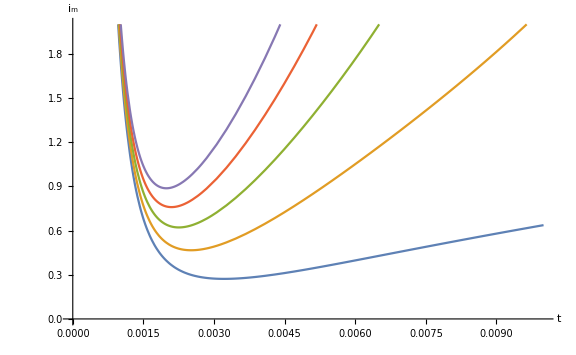

```mathematica
Plot[{
Re[imTDM[1.0,τm,τr,im0,ilr0]]/.{τm->0.01,τr->0.001,im0->foo,ilr0->bar},
Re[imTDM[3.0,τm,τr,im0,ilr0]]/.{τm->0.01,τr->0.001,im0->foo,ilr0->bar},
Re[imTDM[5.0,τm,τr,im0,ilr0]]/.{τm->0.01,τr->0.001,im0->foo,ilr0->bar},
Re[imTDM[7.0,τm,τr,im0,ilr0]]/.{τm->0.01,τr->0.001,im0->foo,ilr0->bar},
Re[imTDM[9.0,τm,τr,im0,ilr0]]/.{τm->0.01,τr->0.001,im0->foo,ilr0->bar}
},{t,0,0.010},
ImageSize->Large,PlotRange->{0,2},AxesLabel->{"t","i_m"}
]
(*Plot[Im[imTDM[iin,τm,τr]],{t,0,tMax},ImageSize->Large,PlotRange->Automatic,AxesLabel->{"t","i_m"}],*)
(*LogPlot[Re[imTDM[iin,τm,τr]],{t,0,tMax},ImageSize->Large,PlotRange->{10^-4,All},AxesLabel->{"t","i_m"}]*)
(*LogPlot[Im[imTDM[iin,τm,τr]],{t,0,tMax},ImageSize->Large,PlotRange->All,AxesLabel->{"t","i_m"}]*)
```

#### Plot how i_m changes with varying τ_m

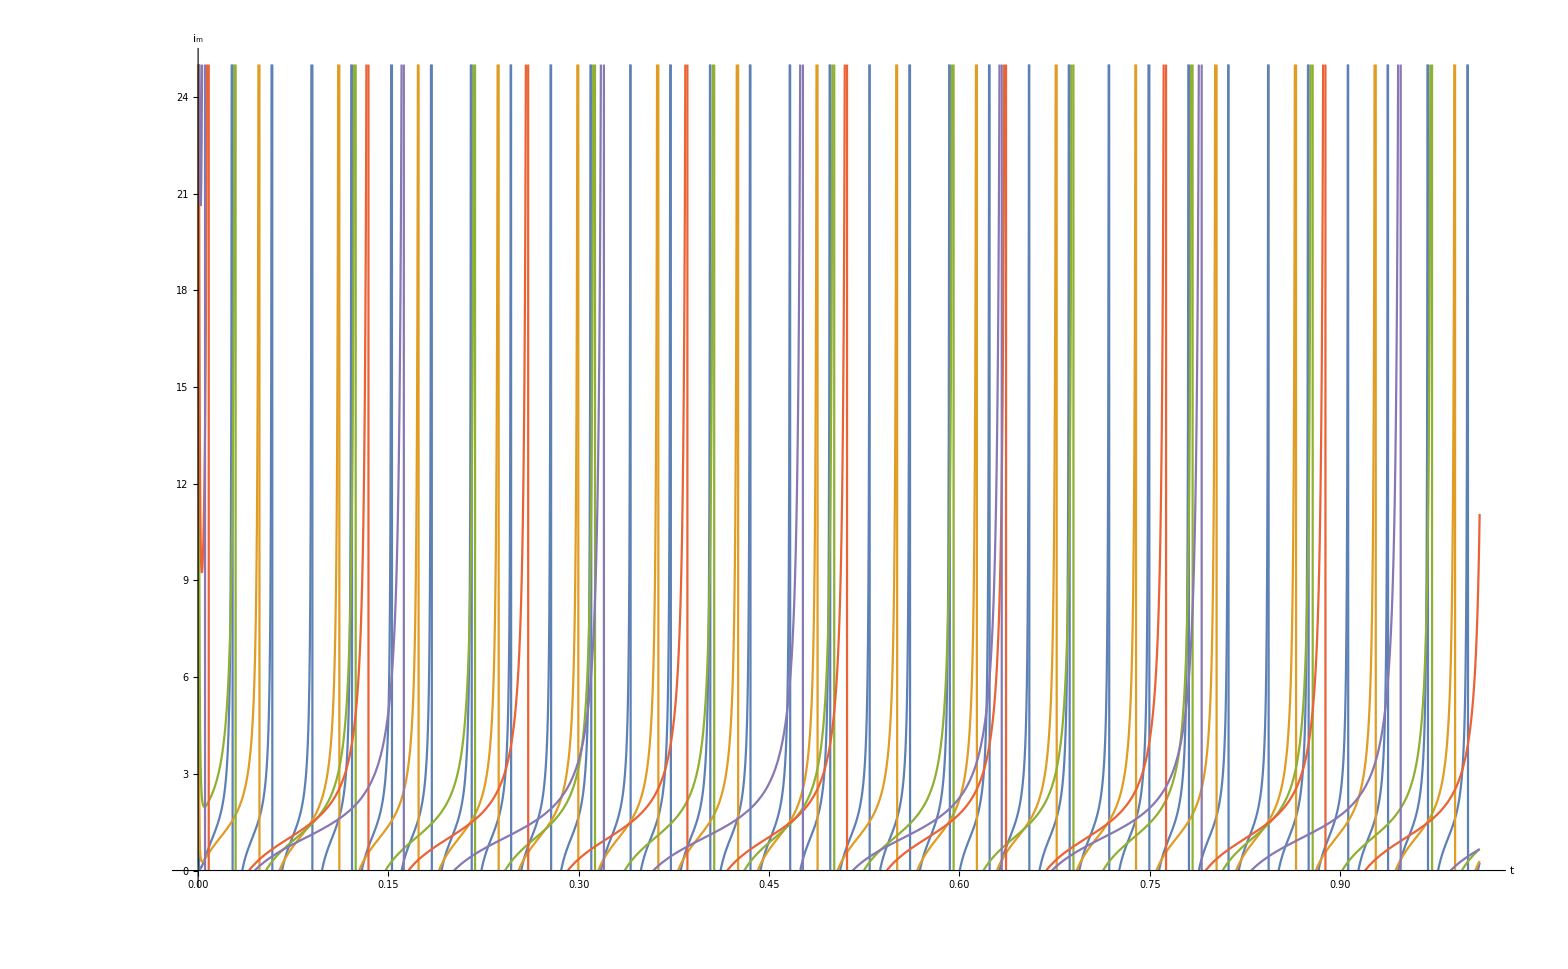

```mathematica
Plot[{
Re[imTDM[iin,0.005,τr,im0,ilr0]]/.{iin->1,τr->0.001,im0->foo,ilr0->bar},
Re[imTDM[iin,0.010,τr,im0,ilr0]]/.{iin->1,τr->0.001,im0->foo,ilr0->bar},
Re[imTDM[iin,0.015,τr,im0,ilr0]]/.{iin->1,τr->0.001,im0->foo,ilr0->bar},
Re[imTDM[iin,0.020,τr,im0,ilr0]]/.{iin->1,τr->0.001,im0->foo,ilr0->bar},
Re[imTDM[iin,0.025,τr,im0,ilr0]]/.{iin->1,τr->0.001,im0->foo,ilr0->bar}
},{t,0,1.01},
ImageSize->Large,PlotRange->{0,25},AxesLabel->{"t","i_m"}
]
(*Plot[Im[imTDM[iin,τm,τr]],{t,0,tMax},ImageSize->Large,PlotRange->Automatic,AxesLabel->{"t","i_m"}],*)
(*LogPlot[Re[imTDM[iin,τm,τr]],{t,0,tMax},ImageSize->Large,PlotRange->{10^-4,All},AxesLabel->{"t","i_m"}]*)
(*LogPlot[Im[imTDM[iin,τm,τr]],{t,0,tMax},ImageSize->Large,PlotRange->All,AxesLabel->{"t","i_m"}]*)
```

#### Plot how i_m changes with varying τ_r

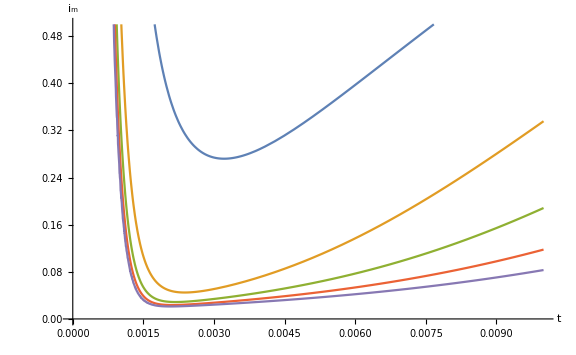

```mathematica
Plot[{
Re[imTDM[iin,τm,0.001,im0,ilr0]]/.{iin->1,τm->0.01,im0->foo,ilr0->bar},
Re[imTDM[iin,τm,0.002,im0,ilr0]]/.{iin->1,τm->0.01,im0->foo,ilr0->bar},
Re[imTDM[iin,τm,0.003,im0,ilr0]]/.{iin->1,τm->0.01,im0->foo,ilr0->bar},
Re[imTDM[iin,τm,0.004,im0,ilr0]]/.{iin->1,τm->0.01,im0->foo,ilr0->bar},
Re[imTDM[iin,τm,0.005,im0,ilr0]]/.{iin->1,τm->0.01,im0->foo,ilr0->bar}
},{t,0,0.01},
ImageSize->Large,PlotRange->{0,0.5},AxesLabel->{"t","i_m"}
]
(*Plot[Im[imTDM[iin,τm,τr]],{t,0,tMax},ImageSize->Large,PlotRange->Automatic,AxesLabel->{"t","i_m"}],*)
(*LogPlot[Re[imTDM[iin,τm,τr]],{t,0,tMax},ImageSize->Large,PlotRange->{10^-4,All},AxesLabel->{"t","i_m"}]*)
(*LogPlot[Im[imTDM[iin,τm,τr]],{t,0,tMax},ImageSize->Large,PlotRange->All,AxesLabel->{"t","i_m"}]*)
```

#### Understanding of how i_m behaves if we include the i_lr_sat portion of i_in

```mathematica
twoDynModelSol1=DSolve[{τm imem'[t]==1/2 imem[t]^2-imem[t](1+ilrsat[t])+iin+ilrsat[t]*10^I01exp ,τr ilrsat'[t]==-ilrsat[t],imem[0]==0,ilrsat[0]==2},{imem[t],ilrsat[t]},t];
imTDM1[iin_,τm_,τr_,I01_]=Simplify[imem[t]/.twoDynModelSol1,τm>0&&τr>0&&iin≥ 0.5&&I01exp>0];
```

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is TraditionalForm` == 0.

General::stop: Further output of Solve :: incnst will be suppressed during this calculation.

Solve::ifun: Inverse functions are being used by TraditionalForm`Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
Subscript[i, m]==imTDM1[Subscript[i, in],Subscript[τ, m],Subscript[τ, r],Subscript[I, 01]]
```

i_m=={-((-ⅈ (√(2 iin-1)-ⅈ) (-10^I01exp τm τr+τm τr+√(-(2 iin-1) τm^2 τr^2))/(2 τm^2)(τm^2+√(-(2 iin-1) τm^2 τr^2))/τm^2(ⅇ^(-t/τr) τr)/τm (ⅇ^(-t/τr))^((ⅈ √(2 iin-1) τr)/τm)-((√(-(2 iin-1) τm^2 τr^2)-(-1+10^I01exp) τm τr) (2 τm^2-10^I01exp τr τm+τr τm+√(-(2 iin-1) τm^2 τr^2))/(2 τm^2)(√(-(2 iin-1) τm^2 τr^2))/τm^2+2(ⅇ^(-t/τr) τr)/τm (ⅇ^(-t/τr))^((ⅈ √(2 iin-1) τr)/τm+1))/(τm^2+√(-(2 iin-1) τm^2 τr^2))-(ⅇ^(-t/τr) (-(√(2 iin-1)-ⅈ) (τm^2+(2 iin-1) τr^2) (√(-(2 iin-1) τm^2 τr^2)-(-1+10^I01exp) τm τr) (-10^I01exp τm τr+τm τr+√(-(2 iin-1) τm^2 τr^2))/(2 τm^2)(τm^2+√(-(2 iin-1) τm^2 τr^2))/τm^2τr/τm-ⅈ τr (-(-2 iin-2^(I01exp+1) 5^I01exp+100^I01exp+2) τr τm^2+2 (-1+10^I01exp) ((2 iin-1) τr^2+√(-(2 iin-1) τm^2 τr^2)) τm-(2 iin+2^(I01exp+1) 5^I01exp-100^I01exp-2) τr √(-(2 iin-1) τm^2 τr^2)) (2 τm^2-10^I01exp τr τm+τr τm+√(-(2 iin-1) τm^2 τr^2))/(2 τm^2)(√(-(2 iin-1) τm^2 τr^2))/τm^2+2τr/τm) (ⅇ^(t/τr) (1-ⅈ √(2 iin-1)) (√(-(2 iin-1) τm^2 τr^2)-τm^2) -((-1+10^I01exp) τm τr+√(-(2 iin-1) τm^2 τr^2))/(2 τm^2)1-(√(-(2 iin-1) τm^2 τr^2))/τm^2(ⅇ^(-t/τr) τr)/τm+((-1+10^I01exp) τm τr+√(-(2 iin-1) τm^2 τr^2)) -(-2 τm^2+(-1+10^I01exp) τr τm+√(-(2 iin-1) τm^2 τr^2))/(2 τm^2)2-(√(-(2 iin-1) τm^2 τr^2))/τm^2(ⅇ^(-t/τr) τr)/τm))/((τm^2-√(-(2 iin-1) τm^2 τr^2)) (ⅈ (10^I01exp (-2+10^I01exp)+2 iin) (τm^2+√(-(2 iin-1) τm^2 τr^2)) -(-2 τm^2+(-1+10^I01exp) τr τm+√(-(2 iin-1) τm^2 τr^2))/(2 τm^2)2-(√(-(2 iin-1) τm^2 τr^2))/τm^2τr/τm τr^2+(√(2 iin-1)+ⅈ) (τm^2+(2 iin-1) τr^2) (√(-(2 iin-1) τm^2 τr^2)-(-1+10^I01exp) τm τr) -((-1+10^I01exp) τm τr+√(-(2 iin-1) τm^2 τr^2))/(2 τm^2)1-(√(-(2 iin-1) τm^2 τr^2))/τm^2τr/τm)))/((-10^I01exp τm τr+τm τr+√(-(2 iin-1) τm^2 τr^2))/(2 τm^2)(τm^2+√(-(2 iin-1) τm^2 τr^2))/τm^2(ⅇ^(-t/τr) τr)/τm (ⅇ^(-t/τr))^((ⅈ √(2 iin-1) τr)/τm)+(((√(2 iin-1)-ⅈ) (τm^2+(2 iin-1) τr^2) (√(-(2 iin-1) τm^2 τr^2)-(-1+10^I01exp) τm τr) (-10^I01exp τm τr+τm τr+√(-(2 iin-1) τm^2 τr^2))/(2 τm^2)(τm^2+√(-(2 iin-1) τm^2 τr^2))/τm^2τr/τm+ⅈ τr (-(-2 iin-2^(I01exp+1) 5^I01exp+100^I01exp+2) τr τm^2+2 (-1+10^I01exp) ((2 iin-1) τr^2+√(-(2 iin-1) τm^2 τr^2)) τm-(2 iin+2^(I01exp+1) 5^I01exp-100^I01exp-2) τr √(-(2 iin-1) τm^2 τr^2)) (2 τm^2-10^I01exp τr τm+τr τm+√(-(2 iin-1) τm^2 τr^2))/(2 τm^2)(√(-(2 iin-1) τm^2 τr^2))/τm^2+2τr/τm) -((-1+10^I01exp) τm τr+√(-(2 iin-1) τm^2 τr^2))/(2 τm^2)1-(√(-(2 iin-1) τm^2 τr^2))/τm^2(ⅇ^(-t/τr) τr)/τm)/(ⅈ (10^I01exp (-2+10^I01exp)+2 iin) (τm^2+√(-(2 iin-1) τm^2 τr^2)) -(-2 τm^2+(-1+10^I01exp) τr τm+√(-(2 iin-1) τm^2 τr^2))/(2 τm^2)2-(√(-(2 iin-1) τm^2 τr^2))/τm^2τr/τm τr^2+(√(2 iin-1)+ⅈ) (τm^2+(2 iin-1) τr^2) (√(-(2 iin-1) τm^2 τr^2)-(-1+10^I01exp) τm τr) -((-1+10^I01exp) τm τr+√(-(2 iin-1) τm^2 τr^2))/(2 τm^2)1-(√(-(2 iin-1) τm^2 τr^2))/τm^2τr/τm)))}

```mathematica
Manipulate[
Grid[{{
Plot[Re[imTDM1[iin,τm,τr,I01exp]],{t,0,tMax},ImageSize->Large,PlotRange->{0,Automatic},AxesLabel->{"t","i_m"}],
(*Plot[Im[im[iin,τm,τr,I01exp]/.{C[1]->1,C[2]->2}],{t,0,tMax},ImageSize->Large,PlotRange->Automatic,AxesLabel->{"t","i_m"}],*)
LogPlot[Re[imTDM1[iin,τm,τr,I01exp]],{t,0,tMax},ImageSize->Large,PlotRange->{10^-4,All},AxesLabel->{"t","i_m"}]
(*,LogPlot[Im[im[iin,τm,τr,I01exp]/.{C[1]->1,C[2]->2}],{t,0,tMax},ImageSize->Large,PlotRange->All,AxesLabel->{"t","i_m"}]*)
}}],
{{iin,1},0.5,10,0.1,Appearance->{"Labeled","Open"}},
{{τm,0.010},0.001,0.10,0.001,Appearance->{"Labeled","Open"}},
{{τr,0.001},0.001,0.01,0.001,Appearance->{"Labeled","Open"}},
{{I01exp,1},-15,0,1,Appearance->{"Labeled","Open"}},
{{tMax,0.5},0.1,2.0,0.1,Appearance->{"Labeled","Open"}}
]
```

This doesn’t result in any new understanding at the moment.  The plots are not plottable right now, either so they also give no insight.  If push comes to shove, I will return to this (as of 4.22.15), but for now, I will just assume that the I_lr_sat portion of i_in is neglible, as assumed in the previous section.

### Derivation of t_r (including I_lk part of initial equation)

This derivation is the result of my lab meeting talk, where Ben pointed out that I made the assumption that I could get rid of α_7/α_B1 I_lk, because the I_b term would dominate the equation.  With that said, this approximation doesn’t need to be made and therefore I could add back a term and rederive the math to see how I_lk further affects the refractory time (t_r).

```mathematica
ImageResize[Import["/home/noza/work/Schematic Pictures/SomaNoAnNoA6WithIrDrawing.png"],400]
```

-Graphics-

Compared to the image above, the following notations are used below:
	I_leak→I_l
	I_bk→I_b
	I_lkr→I_lr

The equation for t_r is superficially (b/c of some assumptions that I make) derived as follows:
Basic equations:
	I_l/α_7=I_lk/α_B1 , current mirror mirroring the leak current
	(I_m I_b)/(α_1 α_10)=(I_lk I_in)/(α_B1 α_B2), using translinear principle to use the biases (I_in and I_lk) to set the output (I_m)
	I_fb/α_4=I_m/α_3, this derivation assumes that transisor A_6 isn’t in the circuit and therefore I_fb is just a mirrored version of I_m
(1)	I_r/α_12=I_ref/α_B3, current mirror for the refractory current
	I_lr=α_8 I_(0_8)ⅇ^((-κ·V_lrgs)/U_t)(1-ⅇ^(V_lrds/U_t)), because this transistor could/would be operating in the linear region during the refractory period
(2)	I_r=(C_r V_r)/t_r, t_r is the actual duration of the refractory period, as opposed to our old theoretical t_ref value which assumed that the capacitor charged to V_dd, 
		instead of the V_r found in this equation.
Derivation:
During the refractory period, we can assume capacitor C_m is charging or fully charged as long as the following condition is true:

(3)	I_l+I_lr>I_b+I_fb

Subsituting from the basic equations above:

	α_7/α_B1 I_lk+I_lr>(α_1 α_10)/(α_B1 α_B2)(I_lk I_in)/I_m+α_4/α_3 I_m
	I_lr>(α_1 α_10)/(α_B1 α_B2)(I_lk I_in)/I_m+α_4/α_3 I_m-α_7/α_B1 I_lk
	
Our first major assumption is that α_4/α_3 I_m can be ignored because during the refractory period I_m is small and therefore the (α_1 α_10)/(α_B1 α_B2)(I_lk I_in)/I_m is large whilie α_4/α_3 I_m is really small.

	I_lr>(α_1 α_10)/(α_B1 α_B2)(I_lk I_in)/I_m-α_7/α_B1 I_lk, it should be noted here that this is the same as saying I_lr>I_b-I_l
	I_lr>(α_1 α_10)/(α_B1 α_B2)(I_lk I_in)/(I_(0_1))-α_7/α_B1 I_lk, through simulation, we found that V_m is almost always reset fully, and as such, I_m is nearly I_(0_1), where I_(0_1)is the leakage current value of transistor A_1
	α_8 I_(0_8)ⅇ^((-κ·V_lrgs)/U_t)(1-ⅇ^(V_lrds/U_t))>(α_1 α_10)/(α_B1 α_B2)(I_lk I_in)/(I_(0_1))-α_7/α_B1 I_lk/(I_(0_8)), expand I_lr
	ⅇ^((-κ·(V_r-V_dd))/U_t)(1-ⅇ^((V_m-V_dd)/U_t))>(α_1 α_10)/(α_B1 α_B2 α_8)(I_lk I_in)/(I_(0_1)I_(0_8))-α_7/α_B1 I_lk/(I_(0_8)), move constants across
	ⅇ^((-κ·(V_r-V_dd))/U_t)>(α_1 α_10)/(α_B1 α_B2 α_8)(I_lk I_in)/(I_(0_1)I_(0_8)(1-ⅇ^((V_m-V_dd)/U_t)))-α_7/α_B1 I_lk/(I_(0_8)(1-ⅇ^((V_m-V_dd)/U_t)))
	(κ·(V_dd-V_r))/U_t>log((α_1 α_10 I_lk I_in)/(α_B1 α_B2 α_8 I_(0_1)I_(0_8)(1-ⅇ^((V_m-V_dd)/U_t)))-α_7/α_B1 I_lk/(I_(0_8)(1-ⅇ^((V_m-V_dd)/U_t)))), take a log of both sides of the equation
	V_dd-V_r>U_t/κ log((α_1 α_10 I_lk I_in)/(α_B1 α_B2 α_8 I_(0_1)I_(0_8)(1-ⅇ^((V_m-V_dd)/U_t)))-α_7/α_B1 I_lk/(I_(0_8)(1-ⅇ^((V_m-V_dd)/U_t))))
	V_r<V_dd-U_t/κ log((α_1 α_10 I_lk I_in)/(α_B1 α_B2 α_8 I_(0_1)I_(0_8)(1-ⅇ^((V_m-V_dd)/U_t)))-α_7/α_B1 I_lk/(I_(0_8)(1-ⅇ^((V_m-V_dd)/U_t))))
	(t_r I_r)/C_r=V_dd-U_t/κ log((α_1 α_10 I_lk I_in)/(α_B1 α_B2 α_8 I_(0_1)I_(0_8)(1-ⅇ^((V_m-V_dd)/U_t)))-α_7/α_B1 I_lk/(I_(0_8)(1-ⅇ^((V_m-V_dd)/U_t)))), substitute V_r→ (t_r I_r)/C_r, as per equation (2) above
	t_r=(C_r V_dd-(C_r U_t)/κ log((α_1 α_10 I_lk I_in)/(α_B1 α_B2 α_8 I_(0_1)I_(0_8)(1-ⅇ^((V_m-V_dd)/U_t)))-α_7/α_B1 I_lk/(I_(0_8)(1-ⅇ^((V_m-V_dd)/U_t)))))/I_r

Substitute I_ref in for I_r, as per equation (1) above, which results in the actual refractory period equation:

t_r=((α_B3 C_r V_dd)/α_12-(α_B3 C_r U_t)/(α_12 κ)log((α_1 α_10 I_lk I_in)/(α_B1 α_B2 α_8 I_(0_1)I_(0_8)(1-ⅇ^((V_m-V_dd)/U_t)))-α_7/α_B1 I_lk/(I_(0_8)(1-ⅇ^((V_m-V_dd)/U_t)))))/I_ref

This implies that our old ρ_ref=(α_B3 C_r V_dd)/α_12equation only accounted for the first term in the real t_ref calculation.  It should now be broken up into four calibration parameters, as per the equations below

t_r=(ρ_ref1-ρ_ref2 log(ρ_ref3 I_lk I_in-ρ_ref4 I_lk))/I_ref
	ρ_ref1=(α_B3 C_r V_dd)/α_12
	ρ_ref2=(α_B3 C_r U_t)/(α_12 κ)
	ρ_ref3=(α_1 α_10)/(α_B1 α_B2 α_8 I_(0_1)I_(0_8)(1-ⅇ^((V_m-V_dd)/U_t)))
	ρ_ref4=α_7/(α_B1 I_(0_8)(1-ⅇ^((V_m-V_dd)/U_t)))

It should be noted that ρ_ref1 is dependent on V_m, which means it isn’t actually a constant.  With that said, from my simulations of the circuit, we see V_m vary between 1.7998 and 1.8003, as τ_m theoretically varies between 0.002s and 0.24s.  In reality, V_m can’t really be greater than 1.8V, or more accurately V_dd.  As such, we can make the assumption that 1-ⅇ^((V_m-V_dd)/U_t) approaches 0 as V_m resets more fully.  Relative to the leakage currents, I_(0_8)and I_(0_1), this quantity ends up being rather large.  The previous statement is based on the assumptions that the leakage currents are on the order of fA (10^-15 A) each, and that 1-ⅇ^((V_m-V_dd)/U_t)is on the order of 10^-4,10^-5,10^-6, or 10^-7.  Therefore the log term which affects ρ_ref3 and ρ_ref4 is dominantly set by the leakage currents, and so any variance in V_m is a minor variance in the overall value of t_r.  As such the t_r equations above are modeled as per the equations below, where p_ref3 and ρ_ref4 are assumed to be a constant:

t_r=(ρ_ref1-ρ_ref2 log(ρ_ref3 I_lk I_in-ρ_ref4 I_lk))/I_ref
	ρ_ref1=(α_B3 C_r V_dd)/α_12
	ρ_ref2=(α_B3 C_r U_t)/(α_12 κ)
	ρ_ref3=(α_1 α_10)/(α_B1 α_B2 α_8 I_(0_1)I_(0_8))
	ρ_ref4=α_7/(α_B1 I_(0_8))

Quadratic soma model manipulators

## Function Definitions

### Conversion functions from dimensionless forms to dimensional currents

```mathematica
iIntoIin[iIn_,Ilk_,pqua_,pilkr_]:=(iIn (Ilk+pilkr)^2)/(pqua Ilk)
iIntoIlkP[iIn_,Iin_,pqua_,pilkr_]:=(√(Iin^2 pqua^2-4 iIn Iin pilkr pqua)-2 iIn pilkr+Iin pqua)/(2 iIn)
iIntoIlkN[iIn_,Iin_,pqua_,pilkr_]:=(-√(Iin^2 pqua^2-4 iIn Iin pilkr pqua)-2 iIn pilkr+Iin pqua)/(2 iIn)
tauToIlk[tau_,ptau_,pilkr_]:=ptau/tau-pilkr
trefToIref[tref_,pref_]:=pref/tref
trToIref[tr_,Iin_,Ilk_,pref1_,pref2_]:=(pref1-pref2 Log[Iin Ilk])/tr
```

#### Derivation of the relation between i_in and I_in or I_lk

Solve for I_in or I_lk in terms of i_in, I_lk/I_in (respectively), ρ_qua, and ρ_ilkr.  These solve equations were used to get the values for iIntoIlkP and iIntoIlkN above.

```mathematica
Solve[pqua ((Iin Ilk)/(Ilk+pilkr)^2)==iIn,Iin]
Solve[pqua ((Iin Ilk)/(Ilk+pilkr)^2)==iIn,Ilk]
```

{{Iin→(iIn (Ilk+pilkr)^2)/(Ilk pqua)}}

{{Ilk→(-√(Iin^2 pqua^2-4 iIn Iin pilkr pqua)-2 iIn pilkr+Iin pqua)/(2 iIn)},{Ilk→(√(Iin^2 pqua^2-4 iIn Iin pilkr pqua)-2 iIn pilkr+Iin pqua)/(2 iIn)}}

#### Test Plot showing I_in to I_lk relation for a given value of i_in

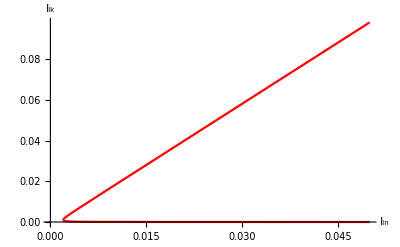

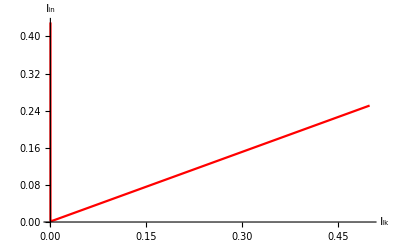

```mathematica
tmpiIn=1.0;
Plot[{iIntoIlkP[tmpiIn,Iin,pquatmp,pilkrtmp],iIntoIlkN[tmpiIn,Iin,pquatmp,pilkrtmp]},{Iin,0,0.05},PlotStyle->Red,AxesLabel->{"I_in","I_lk"}]
Plot[{iIntoIin[tmpiIn,Ilk,pquatmp,pilkrtmp]},{Ilk,0,0.5},PlotStyle->Red,AxesLabel->{"I_lk","I_in"}]
```

### i_in function

iIn is also the equivalent of defining i_in as a function of dimensional units (I_in, I_lk, ρ_qua, and  ρ_ilkr)

```mathematica
iIn[Iin_,Ilk_,pqua_,pilkr_]:=pqua (Iin Ilk)/(Ilk+pilkr)^2
```

### τ function

```mathematica
τ[Ilk_,ptau_,pilkr_]:=ptau/(Ilk+pilkr)
```

### t_ref functions

t_ref is assumed to be a close approximation for the actual amount of time that the neuron stays in refraction.  This is based on the fact that C_r was assumed to charge up to V_dd.  In contrast, t_r is the actual amount of time that the neuron stays in refraction, based on when C_r charges up to a specific V_r corresponding to the point where I_lk+I_lr=I_b+I_fb.  At this point, we can assume that V_m, the membrane voltage, starts to decrease again, and the soma starts its firing process.  The derivation for t_r can be found in the notebook titled “RefractoryPeriodModel.nb”.

```mathematica
tref[Iref_,pref_]:=pref/Iref
tr[Iin_,Ilk_,Iref_,pref1_,pref2_]:=(pref1-pref2 Log[Iin Ilk])/Iref
```

### h(i_in) functions

```mathematica
h[iIn_,β0_,βf_]:=(2 (ArcTan[(βf-1)/(√(2 iIn-1))]-ArcTan[(β0-1)/(√(2 iIn-1))]))/(√(2 iIn-1))
hβ0[iIn_,β0_]:=(π-2ArcTan[(β0-1)/(√(2 iIn-1))])/(√(2 iIn-1))
hβf[iIn_,βf_]:=(2 (ArcTan[(βf-1)/(√(2 iIn-1))]+ArcCot[√(2 iIn-1)]))/(√(2 iIn-1))
h[iIn_]:=(π+2ArcCot[√(2 iIn-1)])/(√(2 iIn-1))
```

### Dynamical systems equation of QIF neuron

```mathematica
imDot[im_,iin_,τ_]:=(1/2 im^2-im + iin)/τ
imDot[im_,Iin_,Ilk_,pqua_,ptau_,pilkr_] :=(1/2 im^2-im + iIn[Iin,Ilk,pqua,pilkr])/τ[Ilk,ptau,pilkr]
```

### Firing rate functions

#### Without refractory period, f_0

f_0=1/(τ·h(i_in)); τ=ρ_tau/(I_lk+ρ_ilkr), h(i_in) is expanded as per some of the h functions above, i_in=(ρ_qua(I_in I_lk))/(I_lk+ρ_ilkr)^2

```mathematica
f0[iIn_,τ_]=1/(τ h[iIn]);
f0[iIn_,β0_,βf_,τ_]=1/(τ h[iIn,β0,βf]);
f0[Iin_,Ilk_,pqua_,ptau_,pilkr_]=1/(τ[Ilk,ptau,pilkr] h[iIn[Iin,Ilk,pqua,pilkr]]);
f0[Iin_,Ilk_,pqua_,ptau_,pilkr_,β0_,βf_]=1/(τ[Ilk,ptau,pilkr] h[iIn[Iin,Ilk,pqua,pilkr],β0,βf]);
```

#### With refractory period, f

f=1/(τ·h(i_in)+t_ref)τ=ρ_tau/(I_lk+ρ_ilkr), h(i_in) is expanded as per some of the h functions above, i_in=(ρ_qua(I_in I_lk))/(I_lk+ρ_ilkr)^2, t_ref=ρ_ref/I_ref

```mathematica
f[iIn_,τ_,tref_]=1/(τ h[iIn]+tref);
f[iIn_,β0_,βf_,τ_,tref_]=1/(τ h[iIn,β0,βf]+tref);
f[Iin_,Ilk_,Iref_,pqua_,ptau_,pilkr_,pref_]=1/(τ[Ilk,ptau,pilkr] h[iIn[Iin,Ilk,pqua,pilkr]]+tref[Iref,pref]);
f[Iin_,Ilk_,Iref_,pqua_,ptau_,pilkr_,pref_,β0_,βf_]=1/(τ[Ilk,ptau,pilkr] h[iIn[Iin,Ilk,pqua,pilkr],β0,βf]+tref[Iref,pref]);
f[Iin_,Ilk_,Iref_,pqua_,ptau_,pilkr_,pref1_,pref2_]=1/(τ[Ilk,ptau,pilkr] h[iIn[Iin,Ilk,pqua,pilkr]]+tr[Iin,Ilk,Iref,pref1,pref2]);
f[Iin_,Ilk_,Iref_,pqua_,ptau_,pilkr_,pref1_,pref2_,β0_,βf_]=1/(τ[Ilk,ptau,pilkr] h[iIn[Iin,Ilk,pqua,pilkr],β0,βf]+tr[Iin,Ilk,Iref,pref1,pref2]);
```

## Dimensionless bifurcation model and quadratic firing rate model

```mathematica
DynamicModule[{iin=.51,tau=.015,tauref=0.001,imMax=5, idotMin = 0,idotMax=20, iInMax=2,fMax = 40, ilitMax=3},
Panel[
Grid[{
{Grid[
{{
Grid[{
{Style["i_in",labelSize],Slider[Dynamic[iin],{0.01,2}],InputField[Dynamic[iin],FieldSize->5]},
{Style["τ_m",labelSize],Slider[Dynamic[tau],{0.001,.050,0.001}],InputField[Dynamic[tau],FieldSize->5]},{Style["t_ref",labelSize],Slider[Dynamic[tauref],{0.001,0.02,0.001}],InputField[Dynamic[tauref],FieldSize->5]}},
Alignment->{Left,Center,Left},Spacings->{{1,1,2},0.5}],
Grid[{
{Style["v_in",labelSize],Panel[Dynamic[iin],Background->LightGray]},
{Style["τ_m",labelSize],Panel[Dynamic[tau],Background->LightGray]},
{Style["t_ref",labelSize],Panel[Dynamic[tauref],Background->LightGray]}},
Alignment->{Left,Left},Spacings->{1,0}],
Grid[{
{Style["f",labelSize],Panel[Dynamic[f[iin,tau, tauref]],Background->LightGray]}
}]
}},Spacings->{5,0}]},
{Grid[
{{
Panel[
Dynamic[
Plot[{imDot[imem,iin,tau]},{imem,0,imMax},PlotRange->{idotMin,idotMax},PlotLabel->Style["Bifurcation Model",titleLabelSize],AxesLabel->{Style["v_m",labelSize],Style["v̇",labelSize]},ImageSize->ImgSize]
]
],
Panel[
Dynamic[
Show[
Plot[{
Piecewise[{{0,iIn≤0},{f[iIn,tau,tauref],iIn>0.5}}],
Piecewise[{{0,iIn≤0},{f[iIn,tau,0],iIn>0.5}}],
f[iin,tau,tauref],
f[iin,tau,0]},
{iIn,0,iInMax},AxesOrigin->{0,0},PlotRange->{0,fMax},PlotLabel->Style["Quadratic Neuron Firing Rate",titleLabelSize],PlotStyle-> {Blue, Darker[Red],{Dashed,Blue},{Dashed,Darker[Red]}},AxesLabel->{Style["v_in",labelSize],Style["f(v_in)",labelSize]},ImageSize->ImgSize],
ListPlot[{{iin,f[iin,tau,0]}},PlotStyle->Darker[Green],PlotMarkers->{"●",Small}],
ListPlot[{{iin,f[iin,tau,tauref]}},PlotStyle->Darker[Green],PlotMarkers->{"●",Small}]
]
]
],
Grid[{
{Style["f_0",labelSize],Panel[Dynamic[f[iin,tau, 0]],Background->LightGray]},
{Style["f",labelSize],Panel[Dynamic[f[iin,tau, tauref]],Background->LightGray]},
{Style["Δf_ref",labelSize],Panel[Dynamic[f[iin,tau, 0]-f[iin,tau, tauref]],Background->LightGray]}
}]
}},
Alignment->{Left,Left,Right}]},
{Grid[
{{
Grid[{
{Style["v_m_max",labelSize],Slider[Dynamic[imMax],{0.,20}],InputField[Dynamic[imMax],FieldSize->5]},
{Style["(v̇)_min",labelSize],Slider[Dynamic[idotMin],{-10,0}],InputField[Dynamic[idotMin],FieldSize->5]},{Style["(v̇)_max",labelSize],Slider[Dynamic[idotMax],{10,200}],InputField[Dynamic[idotMax],FieldSize->5]}},
Alignment->{Left,Center,Left},Spacings->{{1,1,1},0.5}],
Grid[{
{Style["v_in_max",labelSize],Slider[Dynamic[iInMax],{0.5,100}],InputField[Dynamic[iInMax],FieldSize->5]},{Style["f(v_in)_max",labelSize],Slider[Dynamic[fMax],{10,1000}],InputField[Dynamic[fMax],FieldSize->5]}},
Alignment->{Left,Center,Left},Spacings->{{1,1,2},0.5}]
}},
Alignment->{Left,Left,Right},Spacings->{18,0}]}
},Alignment->{Center}]
](*Panel*)
]/.{labelSize->14,titleLabelSize->12,ImgSize->400}
```

## Dual-bias dimensional bifurcation model and quadratic firing rate model

```mathematica
DynamicModule[{Iin=.2,Ilk=.595,Iref=7.333,pqua=0.749205038371,ptau=0.00103391302865,pilkr=0.0057548951055,pref=0.022,pref1=0.0439289072916,pref2=-0.000971636917987,imMax=5, idotMin = 0,idotMax=200, iInMax=2,fMax = 175, ilitMax=3},
Panel[
Grid[{
{Grid[
{{
Grid[{
{Style["I_in",labelSize],Slider[Dynamic[Iin],{0.01,5}],InputField[Dynamic[Iin],FieldSize->5]},{Style["I_lk",labelSize],Slider[Dynamic[Ilk],{0.01,1,0.005}],InputField[Dynamic[Ilk],FieldSize->5]},{Style["I_ref",labelSize],Slider[Dynamic[Iref],{0.01,30}],InputField[Dynamic[Iref],FieldSize->5]}},Alignment->{Left,Center,Left},Spacings->{{1,1,2},0.5}],
Grid[{
{Style["ρ_qua",labelSize],Slider[Dynamic[pqua],{0.5,6}],InputField[Dynamic[pqua],FieldSize->5]},{Style["ρ_tau",labelSize],Slider[Dynamic[ptau],{0.0001,0.005}],InputField[Dynamic[ptau],FieldSize->5]},
{Style["ρ_ilkr",labelSize],Slider[Dynamic[pilkr],{0.0001,0.005}],InputField[Dynamic[pilkr],FieldSize->5]},{Style["ρ_ref",labelSize],Slider[Dynamic[pref],{0.,0.2}],InputField[Dynamic[pref],FieldSize->5]}
},Alignment->{Left,Center,Left},Spacings->{{1,1,2},0.5}],
Grid[{
{Style["ρ_ref1",labelSize],Slider[Dynamic[pref1],{-1.,0.2,0.01}],InputField[Dynamic[pref1],FieldSize->5]},
{Style["ρ_ref2",labelSize],Slider[Dynamic[pref2],{0,3.0,0.01}],InputField[Dynamic[pref2],FieldSize->5]}
},Alignment->{Left,Center,Left},Spacings->{{1,1,2},0.5}],
Grid[{
{Style["i_in",labelSize],Panel[Dynamic[iIn[Iin,Ilk,pqua,pilkr]],Background->LightGray]},{Style["τ_m",labelSize],Panel[Dynamic[τ[Ilk,ptau,pilkr]],Background->LightGray]},{Style["t_ref",labelSize],Panel[Dynamic[tref[Iref,pref]],Background->LightGray]},
{Style["t_r",labelSize],Panel[Dynamic[tr[Iin,Ilk,Iref,pref1,pref2]],Background->LightGray]}
},Alignment->{Left,Left},Spacings->{1,0}]

}},Spacings->{5,0}]},
{Grid[
{{
Panel[
Dynamic[
Plot[{imDot[imem,Iin,Ilk,pqua,ptau,pilkr]},{imem,0,imMax},
PlotRange->{idotMin,idotMax},PlotLabel->Style["Bifurcation Model",titleLabelSize],AxesLabel->{Style["i_m",labelSize],Style["OverDot[i_m]",labelSize]},ImageSize->ImgSize]
]
],
Panel[
Dynamic[
Show[
Plot[{
Piecewise[{{None,curiIn≤0.5},{f[curiIn,τ[Ilk,ptau,pilkr],tref[Iref,pref]],curiIn>0.5}}],
Piecewise[{{None,curiIn≤0.5},{f[curiIn,τ[Ilk,ptau,pilkr],0],curiIn>0.5}}],
Piecewise[{{None,curiIn≤0.5},{f[curiIn,τ[Ilk,ptau,pilkr],tr[iIntoIin[curiIn,Ilk,pqua,pilkr],Ilk,Iref,pref1,pref2]],curiIn>0.5}}],
f[iIn[Iin,Ilk,pqua,pilkr],τ[Ilk,ptau,pilkr],tref[Iref,pref]],
f[iIn[Iin,Ilk,pqua,pilkr],τ[Ilk,ptau,pilkr],0],
f[iIn[Iin,Ilk,pqua,pilkr],τ[Ilk,ptau,pilkr],tr[Iin,Ilk,Iref,pref1,pref2]]
},{curiIn,0,iInMax},
AxesOrigin->{0,0},PlotRange->{0,fMax},PlotLabel->Style["Quadratic Neuron Firing Rate",titleLabelSize],
PlotStyle-> {Blue, Darker[Red],Orange,{Dashed,Blue},{Dashed,Darker[Red]},{Dashed,Orange}},AxesLabel->{Style["i_in",labelSize],Style["f(i_in)",labelSize]},ImageSize->ImgSize],
ListPlot[{{iIn[Iin,Ilk,pqua,pilkr],f[iIn[Iin,Ilk,pqua,pilkr],τ[Ilk,ptau,pilkr],0]}},PlotStyle->Darker[Green],PlotMarkers->{"●",Small}],
ListPlot[{{iIn[Iin,Ilk,pqua,pilkr],f[iIn[Iin,Ilk,pqua,pilkr],τ[Ilk,ptau,pilkr],tref[Iref,pref]]}},PlotStyle->Darker[Green],PlotMarkers->{"●",Small}],
ListPlot[{{iIn[Iin,Ilk,pqua,pilkr],f[iIn[Iin,Ilk,pqua,pilkr],τ[Ilk,ptau,pilkr],tr[Iin,Ilk,Iref,pref1,pref2]]}},PlotStyle->Darker[Green],PlotMarkers->{"●",Small}]
]
]
],
Panel[
Dynamic[
Show[
Plot[{
(*Piecewise[{{0,iIn≤0},{f[iIn,τ[Ilk,ptau,pilkr],tref[Iref,pref]],iIn>0.5}}],
Piecewise[{{0,iIn≤0},{f[iIn,τ[Ilk,ptau,pilkr],0],iIn>0.5}}]*)
f[iIn[Iin,Ilit,pqua,pilkr],τ[Ilit,ptau,pilkr],tref[Iref,pref]],
f[iIn[Iin,Ilit,pqua,pilkr],τ[Ilit,ptau,pilkr],0],
f[iIn[Iin,Ilit,pqua,pilkr],τ[Ilit,ptau,pilkr],tr[Iin,Ilk,Iref,pref1,pref2]]
},{Ilit,0,ilitMax},
AxesOrigin->{0,0},PlotRange->{0,fMax},PlotLabel->Style["Quadratic Neuron Firing Rate",titleLabelSize],
PlotStyle-> {Darker[Red],Blue,Orange},AxesLabel->{Style["I_lk",labelSize],Style["f(I_lk)",labelSize]},ImageSize->ImgSize](*,
ListPlot[{{iIn[Iin,Ilk,pqua],f[iIn[Iin,Ilk,pqua],τ[Ilk,ptau],0]}},PlotStyle->Darker[Green],PlotMarkers->{"●",Small}],
ListPlot[{{iIn[Iin,Ilk,pqua],f[iIn[Iin,Ilk,pqua],τ[Ilk,ptau],tref[Iref,pref]]}},PlotStyle->Darker[Green],PlotMarkers->{"●",Small}]*)
]
]
],
Grid[{
{Style["f_0",labelSize],Panel[Dynamic[f[iIn[Iin,Ilk,pqua,pilkr],τ[Ilk, ptau,pilkr], 0]],Background->LightGray]},
{Style["f_t_ref",labelSize],Panel[Dynamic[f[iIn[Iin,Ilk,pqua,pilkr],τ[Ilk, ptau,pilkr], tref[Iref, pref]]],Background->LightGray]},
{Style["f_t_r",labelSize],Panel[Dynamic[f[iIn[Iin,Ilk,pqua,pilkr],τ[Ilk, ptau,pilkr], tr[Iin,Ilk,Iref, pref1,pref2]]],Background->LightGray]},
{Style["Δf_ref",labelSize],Panel[Dynamic[
f[iIn[Iin,Ilk,pqua,pilkr],τ[Ilk, ptau,pilkr], 0]-f[iIn[Iin,Ilk,pqua,pilkr],τ[Ilk, ptau,pilkr], tref[Iref, pref]]],Background->LightGray]},
{Style["Δf_r",labelSize],Panel[Dynamic[
f[iIn[Iin,Ilk,pqua,pilkr],τ[Ilk, ptau,pilkr], 0]-f[iIn[Iin,Ilk,pqua,pilkr],τ[Ilk, ptau,pilkr], tr[Iin, Ilk,Iref, pref1,pref2]]],Background->LightGray]}
}]
}},
Alignment->{Left,Left,Right}]},
{Grid[
{{
Grid[{
{Style["i_m_max",labelSize],Slider[Dynamic[imMax],{0.,20}],InputField[Dynamic[imMax],FieldSize->5]},
{Style["(i̇)_min",labelSize],Slider[Dynamic[idotMin],{-10,0}],InputField[Dynamic[idotMin],FieldSize->5]},{Style["(i̇)_max",labelSize],Slider[Dynamic[idotMax],{10,200}],InputField[Dynamic[idotMax],FieldSize->5]}},
Alignment->{Left,Center,Left},Spacings->{{1,1,1},0.5}],
Grid[{
{Style["i_in_max",labelSize],Slider[Dynamic[iInMax],{0.5,100}],InputField[Dynamic[iInMax],FieldSize->5]},{Style["f(i_in)_max",labelSize],Slider[Dynamic[fMax],{10,1000}],InputField[Dynamic[fMax],FieldSize->5]}},Alignment->{Left,Center,Left},Spacings->{{1,1,2},0.5}]
}},
Alignment->{Left,Left,Right},Spacings->{18,0}]}
},Alignment->{Center}]
](*Panel*)
]/.{labelSize->12,titleLabelSize->11,ImgSize->350}
```

## Current membrane (i_m) as a function of time

### Dimensionless manipulator

```mathematica
im[t_,iin_,tau_]=imem[t]/.DSolve[{tau imem'[t]==1/2 imem[t]^2-imem[t]+iin,imem[0]==1},imem[t],t]
```

Solve::ifun: Inverse functions are being used by TraditionalForm`Solve, so some solutions may not be found; use Reduce for complete solution information.

{√(2 iin-1) tan((√(2 iin-1) t)/(2 tau))+1}

```mathematica
Manipulate[
Plot[
{im[t,iinM,tauM]},
{t,0.0,tMax}, ImageSize->Large, Ticks->{Range[0,tMax,0.1],Automatic}
],
{{iinM,0.6},0.5,3,Appearance->"Labeled"},
{{tauM,0.010},0.001,0.1,Appearance->"Labeled"},
{{tMax,4.0},1.0,10,Appearance->"Labeled"}
]
```

### Dimensional input currents (I_in, I_lk) used to calculate i_in, but not the soma time constant (τ)

```mathematica
imTau[t_,tau_,Iin_, Ilk_,pqua_,pilkr_]=imem[t]/.DSolve[{tau imem'[t]==1/2(imem[t])^2-imem[t]+iIn[Iin,Ilk,pqua,pilkr], imem[0]==1},imem[t],t];
Manipulate[
Grid[{{
Row[{Text["i_in="],iIn[Iin,Ilk,pqua,pilkr]}]
},{
Plot[imTau[t,tau,Iin,Ilk,pqua,pilkr],
{t,0,10},ImageSize->Large,AxesLabel->{"t","i_m"}
]
}}],
{{tau,.01},0,1,.05,Appearance->"Labeled"},
{{Iin,.1},0.01,.3,.01,Appearance->"Labeled"},
{{Ilk,.1},0.01,.2,.005,Appearance->"Labeled"},
{{pqua,.51},0.5,6,.25,Appearance->"Labeled"},
{{pilkr,0.00051},0.00005,0.005,.00005,Appearance->"Labeled"}
]
```

Solve::ifun: Inverse functions are being used by TraditionalForm`Solve, so some solutions may not be found; use Reduce for complete solution information.

### Dimensional input (I_in, I_lk) used to calculate i_in and τ

```mathematica
imDim[t_,Iin_, Ilk_,pqua_,ptau_,pilkr_]=imem[t]/.DSolve[{τ[Ilk,ptau,pilkr] imem'[t]==1/2(imem[t])^2-imem[t]+iIn[Iin,Ilk,pqua,pilkr], imem[0]==1},imem[t],t];
Manipulate[
Grid[{{
Row[{Text["i_in="],iIn[Iin,Ilk,pqua,pilkr]}]
},{
Row[{Text["τ_m="],τ[Ilk,ptau,pilkr]}]
},{
Plot[imDim[t,Iin,Ilk,pqua,ptau,pilkr],
{t,0,10},ImageSize->Large,AxesLabel->{"t","i_m"}
]
}}],
{{Iin,.1},0.01,.3,.01,Appearance->"Labeled"},
{{Ilk,.1},0.01,.2,.005,Appearance->"Labeled"},
{{pqua,.51},0.5,6,.25,Appearance->"Labeled"},
{{ptau,.001},0.0001,0.003,.0001,Appearance->"Labeled"},
{{pilkr,0.00051},0.00005,0.005,.00005,Appearance->"Labeled"}
]
```

Solve::ifun: Inverse functions are being used by TraditionalForm`Solve, so some solutions may not be found; use Reduce for complete solution information.

## h(i_in) vs i_in plot

```mathematica
Series[h[iIn],{iIn,.5,0}]
```

(√2 π)/(√(vin-0.5))-2+O((vin-0.5)^1)

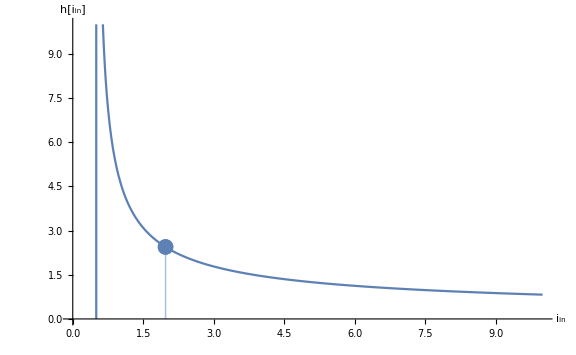

```mathematica
Show[
Plot[h[iIn],{iIn,0,10},
ImageSize->Large,
AxesLabel->{"i_in","h[i_in]"},
PlotRange-> {0,10}],
ListPlot[{{1.97481,h[1.97481]}},Filling->Axis]
]
```

```mathematica
h[.8]
```

6.40988

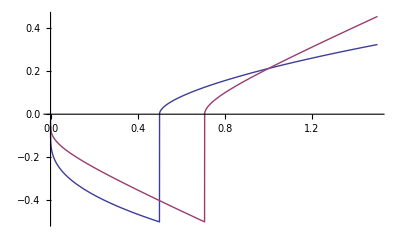

```mathematica
Plot[{h[iIn]^-1,h[(iIn)^2]^-1},{iIn,0,1.5}]
```

Find out at what point the h[i_in] function starts to explode (defined as when the slope is smaller than -1)

```mathematica
h[iin]
h'[iin]
dh[iin]=-(1/(iin (2 iin-1)))-(2 ArcCot[Sqrt[2 iin-1]]+π)/(2 iin-1)^(3/2)
```

(2 cot^-1(√(2 iIn-1))+π)/(√(2 iIn-1))

-1/(iIn (2 iIn-1))-(2 cot^-1(√(2 iIn-1))+π)/(2 iIn-1)^(3/2)

-1/(iIn (2 iIn-1))-(2 cot^-1(√(2 iIn-1))+π)/(2 iIn-1)^(3/2)

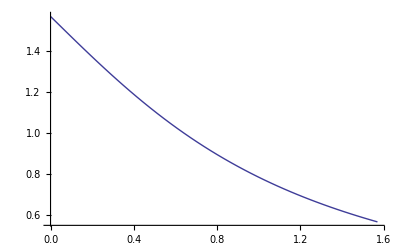

```mathematica
Plot[ArcCot[b],{b,0,π/2}]
```

```mathematica
FindRoot[dh[iin]==-1,{iin,1.5}]
```

{vin→1.97481}

```mathematica
h[{1.7,1.6, 0.6}]/0.03
```

{92.2631,97.2644,405.631}

```mathematica
Limit[h'[iin],iin->∞]
```

0

```mathematica
Limit[1/h[iin],iin->∞]
```

∞

```mathematica
Limit[1/dh[iin],iin->0.5]
```

0.

```mathematica
D[h[iin]^-2, iin]/.iin->{0.5,0.51,0.52}
```

{0.0506606,0.0580795,0.0614491}

## Appendix

### Investigation into discontinuous model fits during calibration

While calibrating Chip 3 of endeavour, I found that using the firing rate including t_ref calibration model, the output theoretical curves had some discontinuities for large I_lk and large I_in, when i_in is still relatively small.  In other words, when the firing rate was small, for some of the larger I_in and I_lk values, we saw that the curve breaks shape and has a steeper, linear looking slope.  I wanted to model this in Mathematica to see if it’s a real effect caused by the t_ref compensation term or if it’s something that python is interpolating incorrectly for some reason.

Resolution: It was found that this effect was happening because of a minor error in the python script which caused the plotting of the equation to be linearized due to improper discretization.

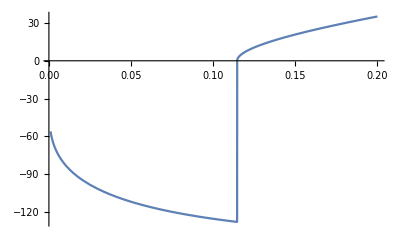

```mathematica
Plot[f[Iin,Ilk,Iref,pqua,ptau,pilkr,pref1,pref2]/.{Ilk->0.182,Iref->1000,pqua->0.86327991, ptau->0.00093283,pilkr->0.00774582,pref1->-6.46045381,pref2->2.18765869},{Iin,0.001,.20}]
```

### Investigation into effects on FI curve if current is bounded by C_max or C_min

```mathematica
Manipulate[
Grid[{
{
Plot[{
Piecewise[{
{None,curiIn≤0.5},
{f[curiIn,tau,0],curiIn>0.5}
}],
(*ADD CODE that converts tref to an Iref value and caps it if it exceeds Subscript[C, max] or is below Subscript[C, min]*)
Piecewise[{
{None,curiIn≤0.5},
{f[curiIn,tau,tr[iIntoIin[curiIn,tauToIlk[tau,ptau,pilkr],pqua,pilkr],tauToIlk[tau,ptau,pilkr],Clip[trToIref[tref1,iIntoIin[curiIn,tauToIlk[tau,ptau,pilkr],pqua,pilkr],tauToIlk[tau,ptau,pilkr],pref1,pref2],{Cmin,Cmax}],pref1,pref2]],curiIn>0.5}
}]
},{curiIn,0,iInMax},
AxesOrigin->{0,0},PlotRange->{0,fMax},PlotLabel->Style["Quadratic Neuron Firing Rate",titleLabelSize],
PlotStyle-> {{Darker[Red],Dashed},Orange},AxesLabel->{Style["i_in",labelSize],Style["f(i_in)",labelSize]},ImageSize->ImgSize]
,
Plot[{
tref1,
tr[iIntoIin[curiIn,tauToIlk[tau,ptau,pilkr],pqua,pilkr],tauToIlk[tau,ptau,pilkr],Clip[trToIref[tref1,iIntoIin[curiIn,tauToIlk[tau,ptau,pilkr],pqua,pilkr],tauToIlk[tau,ptau,pilkr],pref1,pref2],{Cmin,Cmax}],pref1,pref2],
(*tr[iIntoIin[curiIn,tauToIlk[tau,ptau,pilkr],pqua,pilkr],tauToIlk[tau,ptau,pilkr],Cmin,pref1,pref2]*)(*,
tr[iIntoIin[curiIn,tauToIlk[tau,ptau,pilkr],pqua,pilkr],tauToIlk[tau,ptau,pilkr],Cmax,pref1,pref2]*)
},{curiIn,0,3},
ImageSize->ImgSize,PlotRange->{-.0001,3*tref1},PlotStyle->{Dashed,Solid},AxesLabel->{"i_in","t_r"},
Epilog->Inset[
Plot[
tr[iIntoIin[curiIn,tauToIlk[tau,ptau,pilkr],pqua,pilkr],tauToIlk[tau,ptau,pilkr],Clip[trToIref[tref1,iIntoIin[curiIn,tauToIlk[tau,ptau,pilkr],pqua,pilkr],tauToIlk[tau,ptau,pilkr],pref1,pref2],{Cmin,Cmax}],pref1,pref2],
{curiIn,0,3},
PlotRange->{-0.001,0.001},ImageSize->ImgSize/2],
{2.5,0.0002}
]
],
Plot[
pref1-pref2 Log[iIntoIin[curiIn, tauToIlk[tau,ptau,pilkr],pqua,pilkr] tauToIlk[tau,ptau,pilkr]],
{curiIn,0,3},
ImageSize->ImgSize,PlotRange->{-5,5},AxesLabel->{"i_in","p_ref1-p_ref2*log(I_inI_lk)"}
]
},{
Grid[
{
{
tref1,
tr[iIntoIin[curiIn,tauToIlk[tau,ptau,pilkr],pqua,pilkr],tauToIlk[tau,ptau,pilkr],Clip[trToIref[tref1,iIntoIin[curiIn,tauToIlk[tau,ptau,pilkr],pqua,pilkr],tauToIlk[tau,ptau,pilkr],pref1,pref2],{Cmin,Cmax}],pref1,pref2],
tr[iIntoIin[curiIn,tauToIlk[tau,ptau,pilkr],pqua,pilkr],tauToIlk[tau,ptau,pilkr],Cmin,pref1,pref2],
tr[iIntoIin[curiIn,tauToIlk[tau,ptau,pilkr],pqua,pilkr],tauToIlk[tau,ptau,pilkr],Cmax,pref1,pref2]
},
{
trToIref[tref1,iIntoIin[curiIn,tauToIlk[tau,ptau,pilkr],pqua,pilkr],tauToIlk[tau,ptau,pilkr],pref1,pref2],
Clip[trToIref[tref1,iIntoIin[curiIn,tauToIlk[tau,ptau,pilkr],pqua,pilkr],tauToIlk[tau,ptau,pilkr],pref1,pref2],{Cmin,Cmax}]
}
}]
}}
]
,
{{curiIn,1.15},0,3,0.001, Appearance->"Open"},
{{iInMax,2},1,5,0.01},
{{fMax,100},50,500,1}
]/.{tau->0.010,tref1->0.0001,pqua->0.745379,ptau->0.00103434,pilkr->0.00574933,pref1->0.043937,pref2->0.00097134,Cmin->0.000035465, Cmax->3131.22,labelSize->12,titleLabelSize->11,ImgSize->350}
```

## Play Section

```mathematica
tr[0.194914,0.232714,13.997,-0.06314637,0.36832799,18.50241418]
```

0.0000999981

```mathematica
D[B1/(B2+B3 B[t])*A[t],t]
D[(2 α4 αB1)/(α3(α7 Ilk+αB1 Ilrsat[t]))*Iout[t],t]
```

(B1 A'(t))/(B3 B(t)+B2)-(B1 B3 A(t) B'(t))/(B3 B(t)+B2)^2

(2 α4 αB1 Iout'(t))/(α3 (α7 Ilk+αB1 Ilrsat(t)))-(2 α4 αB1^2 Iout(t) Ilrsat'(t))/(α3 (α7 Ilk+αB1 Ilrsat(t))^2)

```mathematica
DSolve[tau im'[t]== iin+1/2 (im[t])^2-im[t] -i8 im[t](1-β2 i1)e^(k/ut(Vdd-β3 t)), im[t],t]
```

Solve::ifun: Inverse functions are being used by TraditionalForm`Solve, so some solutions may not be found; use Reduce for complete solution information.

DSolve[tau im'(t)==-i8 im(t) (β1-β2 i1) e^((k (Vdd-β3 t))/ut)+iin+(im(t))^2/2-im(t),im(t),t]

```mathematica
DSolve[{
tau im'[t]== iin+1/2 (im[t])^2-im[t] -im[t](1-β2 i1)ilr[t],
taur ilr'[t]==-ilr[t] ir, 
im[0]==im0, 
ilr[0]==ilr0},
 {im[t], ilr[t]},t]
```

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is TraditionalForm` == 0.

General::stop: Further output of Solve :: incnst will be suppressed during this calculation.

Solve::ifun: Inverse functions are being used by TraditionalForm`Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ilr(t)→ⅇ^(-(ir t)/taur) ilr0,im(t)→-((2 tau ((ⅈ^((2 ⅈ 1 taur)/(ir tau)) 5 (2 3 taur-1)^((ⅈ 11taur)/(ir tau)))/(-ⅈ im0 ir^3 taur taur/(2 ir tau)-(√(ir^2 tau^2 taur^2-2 iin ir^2 tau^2 taur^2))/(2 ir^2 tau^2)1-(√(ir^2 tau^2 taur^2-2 iin ir^2 tau^2 taur^2))/(ir^2 tau^2)(2 ilr0 ir tau taur-2 i1 ilr0 ir tau taur β2)/(2 ir^2 tau^2) tau^3+√(2 iin-1) ir^3 taur taur/(2 ir tau)-(√(ir^2 tau^2 taur^2-2 iin ir^2 tau^2 taur^2))/(2 ir^2 tau^2)1-(√(ir^2 tau^2 taur^2-2 iin ir^2 tau^2 taur^2))/(ir^2 tau^2)(2 ilr0 ir tau taur-2 i1 ilr0 ir tau taur β2)/(2 ir^2 tau^2) tau^3+28+2 ⅈ iin ilr0 taur^2 √(-(2 iin-1) ir^2 tau^2 taur^2) taur/(2 ir tau)-(√(ir^2 tau^2 taur^2-2 iin ir^2 tau^2 taur^2))/(2 ir^2 tau^2)+12-(√(ir^2 tau^2 taur^2-2 iin ir^2 tau^2 taur^2))/(ir^2 tau^2)(2 ilr0 ir tau taur-2 i1 ilr0 ir tau taur β2)/(2 ir^2 tau^2))-1/taur-1))/((ⅈ^((2 ⅈ 1 taur)/(ir tau)+1) 2^1 4 (1) (ⅇ^-1)^(1/1))/(-ⅈ im0 ir^3 taur taur/(2 ir tau)-(√(ir^2 tau^2 taur^2-2 iin ir^2 tau^2 taur^2))/(2 ir^2 tau^2)1-(√(ir^2 tau^2 taur^2-2 iin ir^2 tau^2 taur^2))/(ir^2 tau^2)(2 ilr0 ir tau taur-2 i1 ilr0 ir tau taur β2)/(2 ir^2 tau^2) tau^3+√(2 iin-1) ir^3 taur taur/(2 ir tau)-(√(ir^2 tau^2 taur^2-2 iin ir^2 tau^2 taur^2))/(2 ir^2 tau^2)1-(√(ir^2 tau^2 taur^2-2 iin ir^2 tau^2 taur^2))/(ir^2 tau^2)(2 ilr0 ir tau taur-2 i1 ilr0 ir tau taur β2)/(2 ir^2 tau^2) tau^3+28+2 ⅈ iin ilr0 taur^2 √(-(2 iin-1) ir^2 tau^2 taur^2) taur/(2 ir tau)-(√(ir^2 tau^2 taur^2-2 iin ir^2 tau^2 taur^2))/(2 ir^2 tau^2)+12-(√(ir^2 tau^2 taur^2-2 iin ir^2 tau^2 taur^2))/(ir^2 tau^2)(2 ilr0 ir tau taur-2 i1 ilr0 ir tau taur β2)/(2 ir^2 tau^2))+ⅈ^1 5 1))}}
 |  |  |  |

```mathematica
D[x^(1+1/κ)/(x^(1/κ)(α+β)-α(γ^(1/κ))),x]
```

((1/κ+1) x^(1/κ))/((α+β) x^(1/κ)-α γ^(1/κ))-((α+β) x^(2/κ))/(κ ((α+β) x^(1/κ)-α γ^(1/κ))^2)

## Old/Obsolete

## Stacked Bias formulation

τ_m i_m^•= -v_m+v_m^2/2+ v_in
i_in=ρ_qua(I_c^2/I_l^2)

```mathematica
VmdotTheory[Vm_,iin_,τ_]:=(1/2 Vm^2-Vm + iin)/τ
VmdotStackedBias[Vm_,Ic_,Il_,τ_,pqua_] :=(1/2 Vm^2-Vm + VinStackedBias[Ic,Il,pqua])/τ
VinStackedBias[Ic_,Il_,pqua_]:=pqua(Ic/Il)^2
τOBS[Il_,ptau_]:=ptau/Il
trefOBS[Iref_,pref_]:=pref/Iref
```

This method of calculating the biases is the method that was used in Peiran’s paper where I_bk was created using two transistors stacked on each other such that you would get I_bk^2.  This method isn’t as clean/interesting as the new method which automatically scales I_in with I_lk.

```mathematica
DynamicModule[{Ic=.5,Il=.595,Iref=7.333,pqua=1.50316,ptau=0.00119,pref=0.022, imMax=5, idotMin = 0,idotMax=20, iInMax=2,fMax = 175, ilitMax=3},
Panel[
Grid[{
{Grid[
{{
Grid[{
{Style["I_c",labelSize],Slider[Dynamic[Ic],{0.01,5}],InputField[Dynamic[Ic],FieldSize->5]},{Style["I_l",labelSize],Slider[Dynamic[Il],{0.01,1,0.005}],InputField[Dynamic[Il],FieldSize->5]},{Style["I_ref",labelSize],Slider[Dynamic[Iref],{0.01,10}],InputField[Dynamic[Iref],FieldSize->5]}},Alignment->{Left,Center,Left},Spacings->{{1,1,2},0.5}],
Grid[{
{Style["ρ_qua",labelSize],Slider[Dynamic[pqua],{0.5,6}],InputField[Dynamic[pqua],FieldSize->5]},{Style["ρ_tau",labelSize],Slider[Dynamic[ptau],{0.0001,0.005}],InputField[Dynamic[ptau],FieldSize->5]},{Style["ρ_ref",labelSize],Slider[Dynamic[pref],{0.,0.2}],InputField[Dynamic[pref],FieldSize->5]}},Alignment->{Left,Center,Left},Spacings->{{1,1,2},0.5}],
Grid[{
{Style["v_in",labelSize],Panel[Dynamic[VinStackedBias[Ic,Il,pqua]],Background->LightGray]},{Style["τ_m",labelSize],Panel[Dynamic[τOBS[Il,ptau]],Background->LightGray]},{Style["t_ref",labelSize],Panel[Dynamic[trefOBS[Iref,pref]],Background->LightGray]}},Alignment->{Left,Left},Spacings->{1,0}],
Grid[{
{Style["f",labelSize],Panel[Dynamic[f[VinStackedBias[Ic,Il,pqua],τOBS[Il, ptau], trefOBS[Iref, pref]]],Background->LightGray]}
}]
}},Spacings->{5,0}]},
{Grid[
{{
Panel[
Dynamic[
Plot[{VmdotStackedBias[Vmem,Ic,Il,τOBS[Il,ptau],pqua]},{Vmem,0,imMax},PlotRange->{idotMin,idotMax},PlotLabel->Style["Bifurcation Model",titleLabelSize],AxesLabel->{Style["v_m",labelSize],Style["v̇",labelSize]},ImageSize->ImgSize]
]
],
Panel[
Dynamic[
Show[
Plot[{
Piecewise[{{0,iIn≤0},{f[iIn,τOBS[Il,ptau],trefOBS[Iref,pref]],iIn>0.5}}],
Piecewise[{{0,iIn≤0},{f[iIn,τOBS[Il,ptau],0],iIn>0.5}}],
f[VinStackedBias[Ic,Il,pqua],τOBS[Il,ptau],trefOBS[Iref,pref]],
f[VinStackedBias[Ic,Il,pqua],τOBS[Il,ptau],0]},
{iIn,0,iInMax},AxesOrigin->{0,0},PlotRange->{0,fMax},PlotLabel->Style["Quadratic Neuron Firing Rate",titleLabelSize],PlotStyle-> {Blue, Darker[Red],{Dashed,Blue},{Dashed,Darker[Red]}},AxesLabel->{Style["v_in",labelSize],Style["f(v_in)",labelSize]},ImageSize->ImgSize],
ListPlot[{{VinStackedBias[Ic,Il,pqua],f[VinStackedBias[Ic,Il,pqua],τOBS[Il,ptau],0]}},PlotStyle->Darker[Green],PlotMarkers->{"●",Small}],
ListPlot[{{VinStackedBias[Ic,Il,pqua],f[VinStackedBias[Ic,Il,pqua],τOBS[Il,ptau],trefOBS[Iref,pref]]}},PlotStyle->Darker[Green],PlotMarkers->{"●",Small}]
]
]
],
Panel[
Dynamic[
Show[
Plot[{
(*Piecewise[{{0,iIn≤0},{f[iIn,τOBS[Il,ptau],trefOBS[Iref,pref]],iIn>0.5}}],
Piecewise[{{0,iIn≤0},{f[iIn,τOBS[Il,ptau],0],iIn>0.5}}]*)
f[VinStackedBias[Ic,Ilit,pqua],τOBS[Ilit,ptau],trefOBS[Iref,pref]],
f[VinStackedBias[Ic,Ilit,pqua],τOBS[Ilit,ptau],0]},
{Ilit,0,ilitMax},AxesOrigin->{0,0},PlotRange->{0,fMax},PlotLabel->Style["Quadratic Neuron Firing Rate",titleLabelSize],PlotStyle-> {Darker[Red],Blue},AxesLabel->{Style["I_lk",labelSize],Style["f(I_lk)",labelSize]},ImageSize->ImgSize](*,
ListPlot[{{VinStackedBias[Ic,Il,pqua],f[VinStackedBias[Ic,Il,pqua],τOBS[Il,ptau],0]}},PlotStyle->Darker[Green],PlotMarkers->{"●",Small}],
ListPlot[{{VinStackedBias[Ic,Il,pqua],f[VinStackedBias[Ic,Il,pqua],τOBS[Il,ptau],trefOBS[Iref,pref]]}},PlotStyle->Darker[Green],PlotMarkers->{"●",Small}]*)
]
]
],
Grid[{
{Style["f_0",labelSize],Panel[Dynamic[f[VinStackedBias[Ic,Il,pqua],τOBS[Il, ptau], 0]],Background->LightGray]},
{Style["f",labelSize],Panel[Dynamic[f[VinStackedBias[Ic,Il,pqua],τOBS[Il, ptau], trefOBS[Iref, pref]]],Background->LightGray]},
{Style["Δf_ref",labelSize],Panel[Dynamic[f[VinStackedBias[Ic,Il,pqua],τOBS[Il, ptau], 0]-f[VinStackedBias[Ic,Il,pqua],τOBS[Il, ptau], trefOBS[Iref, pref]]],Background->LightGray]}
}]
}},
Alignment->{Left,Left,Right}]},
{Grid[
{{
Grid[{
{Style["i_m_max",labelSize],Slider[Dynamic[imMax],{0.,20}],InputField[Dynamic[imMax],FieldSize->5]},
{Style["(i̇)_min",labelSize],Slider[Dynamic[idotMin],{-10,0}],InputField[Dynamic[idotMin],FieldSize->5]},{Style["(i̇)_max",labelSize],Slider[Dynamic[idotMax],{10,200}],InputField[Dynamic[idotMax],FieldSize->5]}},
Alignment->{Left,Center,Left},Spacings->{{1,1,1},0.5}],
Grid[{
{Style["i_in_max",labelSize],Slider[Dynamic[iInMax],{0.5,100}],InputField[Dynamic[iInMax],FieldSize->5]},{Style["f(i_in)_max",labelSize],Slider[Dynamic[fMax],{10,1000}],InputField[Dynamic[fMax],FieldSize->5]}},
Alignment->{Left,Center,Left},Spacings->{{1,1,2},0.5}]
}},
Alignment->{Left,Left,Right},Spacings->{18,0}]}
},Alignment->{Center}]
](*Panel*)
]/.{labelSize->14,titleLabelSize->11,ImgSize->300}
```